## Introduction

Model with J = - K

## Main

### Equations

#### Defintions

```mathematica
Clear[b,j,k,e,xp,xm,θp,θm];
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->-k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

#### Prepare

```mathematica
tempSub=Solve[es[[{1,3}]]=={0,0},{xm,θm}]/.C[1]->0/.C[2]->0;
TableForm[tempSub]
```

xm→π-ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→π-ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
TableForm[etemp]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

#### Order parameter definition

```mathematica
e3={xp==1/2(x1+x2),xm==1/2(x1-x2),θp==1/2(θ1+θ2),θm==1/2(θ1-θ2)};
sub3=Solve[e3,{x1,x2,θ1,θ2}];
Wp=1/2(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)]);
Wm=1/2(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)]);
{Wp,Wm}=({Wp,Wm}/.sub3[[1]])//ExpToTrig//FullSimplify;
Wm=ExpToTrig[Wm]//Simplify;
TableForm[{Wp,Wm}]
```

Cos[xm+θm] (Cos[xp+θp]+ⅈ Sin[xp+θp])
Cos[xm-θm] (Cos[xp-θp]+ⅈ Sin[xp-θp])

### Fixed point 1

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e11={etemp[[1,2]],etemp[[2,1]]}//FullSimplify;
TableForm[e11]
fp1=Solve[e11==0,{xp,θp}]//FullSimplify
Length[fp1]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcCos[-e]},{xp→-ArcCos[-e],θp→ArcCos[-e]},{xp→-ArcCos[-e],θp→-ArcCos[e]},{xp→-ArcCos[-e],θp→ArcCos[e]},{xp→ArcCos[-e],θp→-ArcCos[-e]},{xp→ArcCos[-e],θp→ArcCos[-e]},{xp→ArcCos[-e],θp→-ArcCos[e]},{xp→ArcCos[-e],θp→ArcCos[e]},{xp→-ArcCos[e],θp→-ArcCos[-e]},{xp→-ArcCos[e],θp→ArcCos[-e]},{xp→-ArcCos[e],θp→-ArcCos[e]},{xp→-ArcCos[e],θp→ArcCos[e]},{xp→ArcCos[e],θp→-ArcCos[-e]},{xp→ArcCos[e],θp→ArcCos[-e]},{xp→ArcCos[e],θp→-ArcCos[e]},{xp→ArcCos[e],θp→ArcCos[e]}}

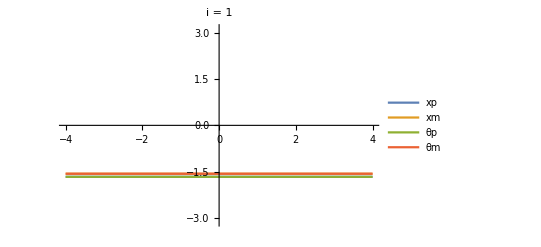
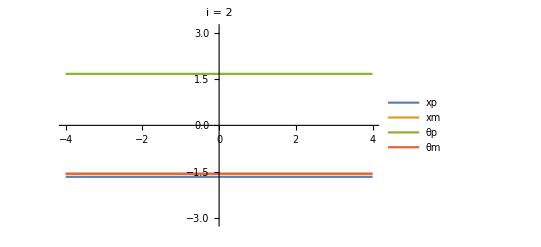
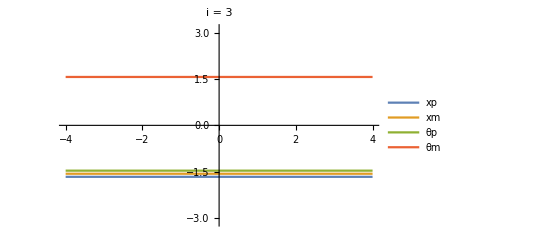
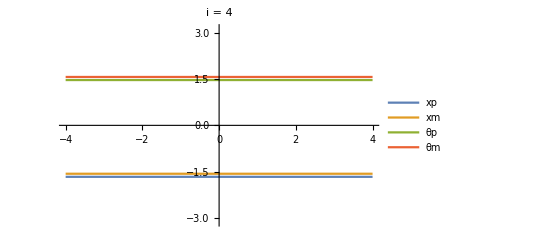
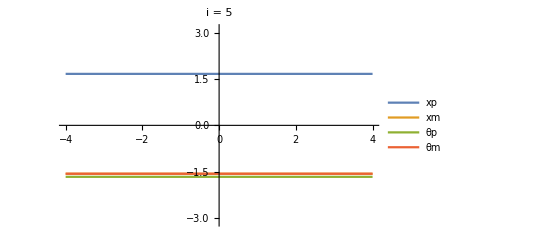
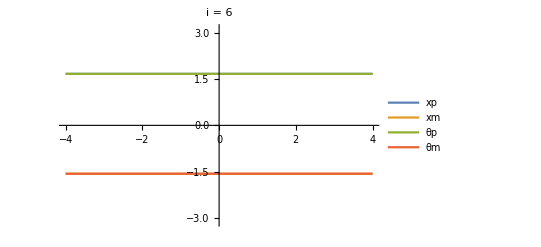
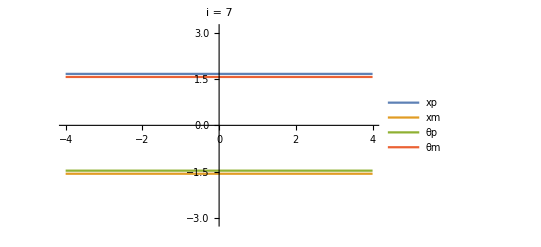
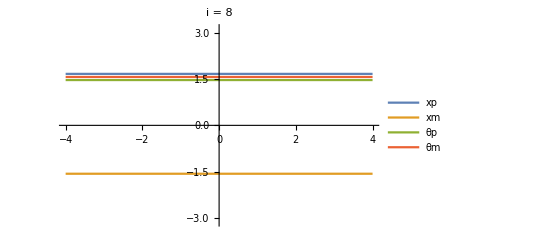

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp1]}]
```

#### Eigenvalues

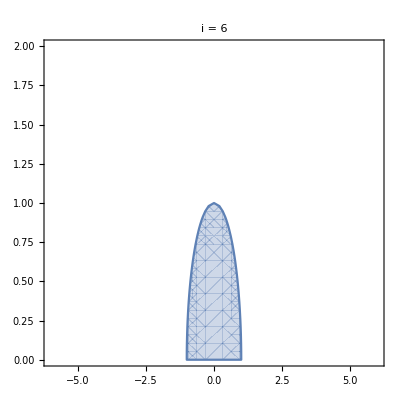
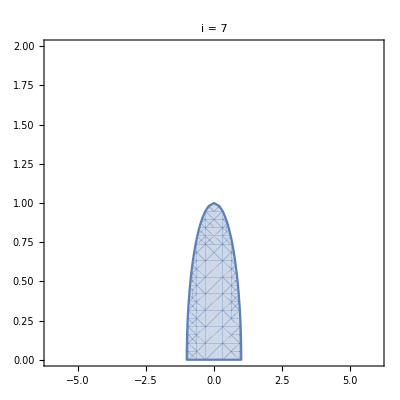
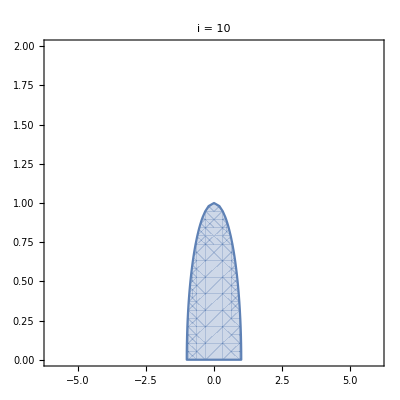
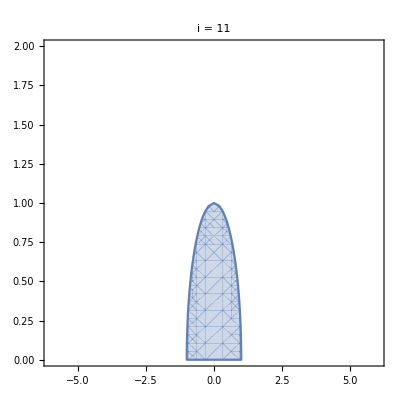
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp1]}
]
```

```mathematica
is={6,7,10,11}
```

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-√(1-e^2)
-√(1-e^2)-k
-√(1-e^2)+k

```mathematica
Solve[λ[[3]]==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

```mathematica
Solve[λ[[4]]==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

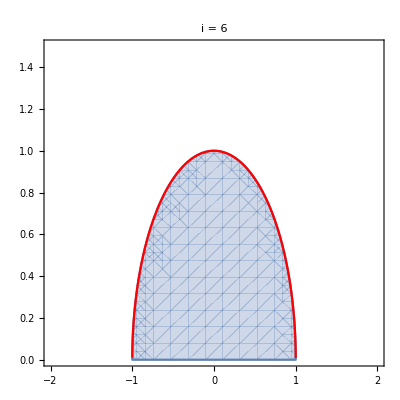

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-2,2},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];
p2=Plot[√(1-k^2),{k,-2,2},PlotStyle->{Red}];
Show[{p1,p2}]
```

#### Order parameter

```mathematica
i=6;
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp1,Wm1}]
```

1-2 e^2+2 ⅈ e √(1-e^2)
1

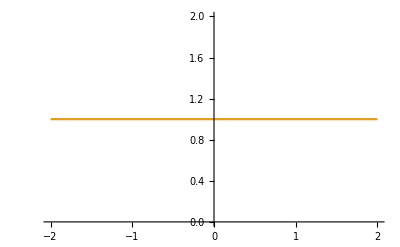

```mathematica
Plot[{Abs[Wp1],Abs[Wm1]},{k,-2,2}]
```

```mathematica
$Assumptions={};
ParallelTable[
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
ContourPlot[{S==Abs[Wp1]/.e->0.1,S==Abs[Wm1]/.e->0.1},{k,-5,5},{S,0,1},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15],
{i,1,Length[fp1]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Fixed point 2

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,2]],etemp[[2,2]]}//FullSimplify;
TableForm[e3]
fp2=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp2]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]}}

32

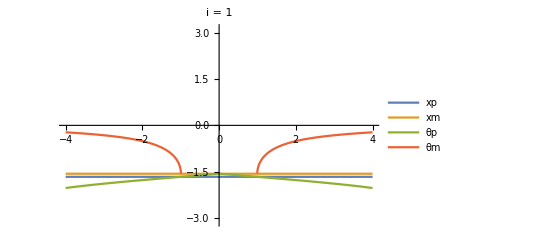
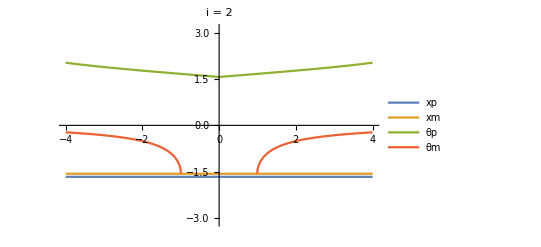
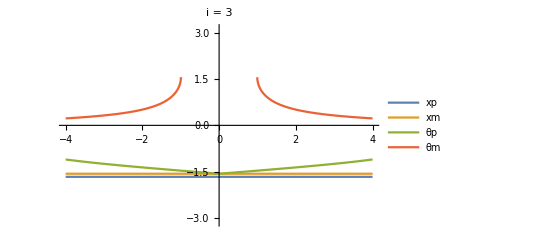
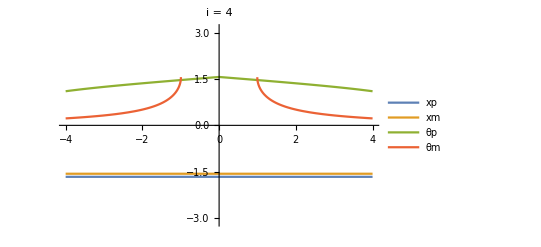
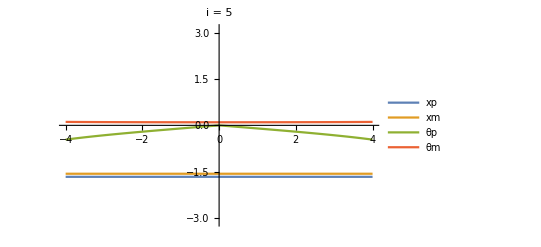
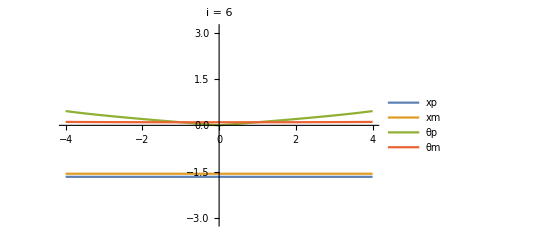
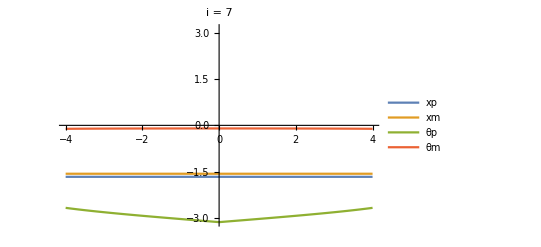
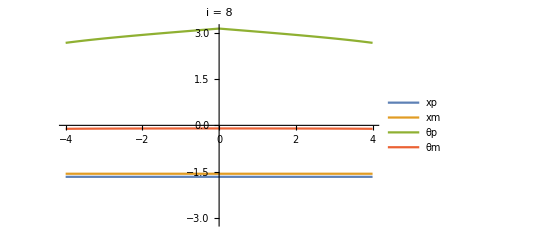

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}]
```

#### Eigenvalues

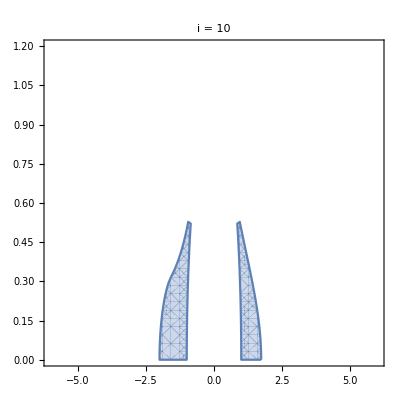
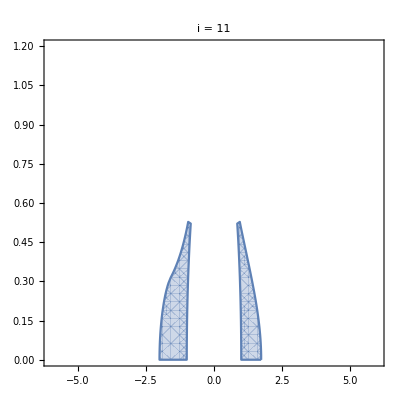
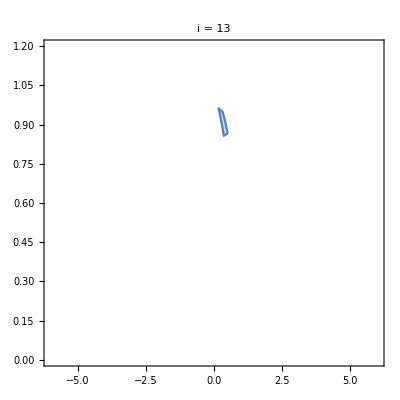
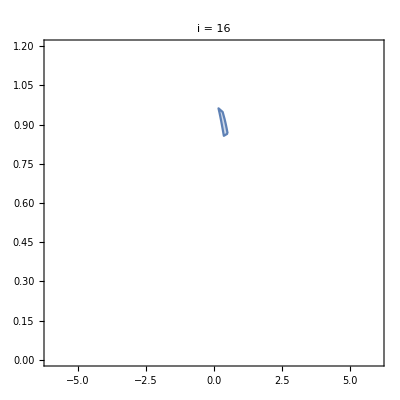
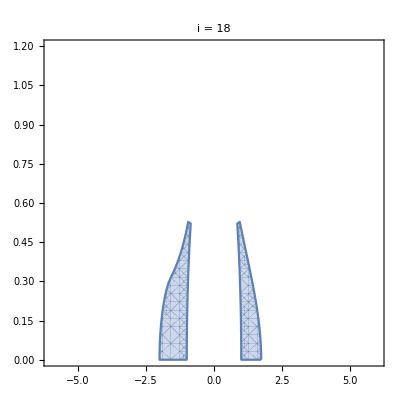
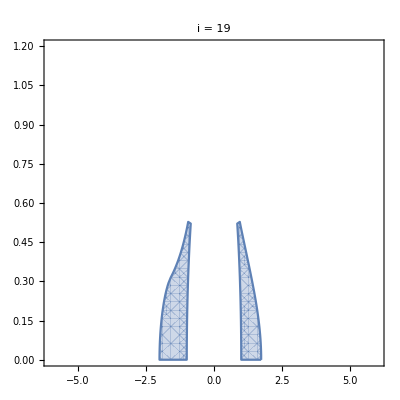
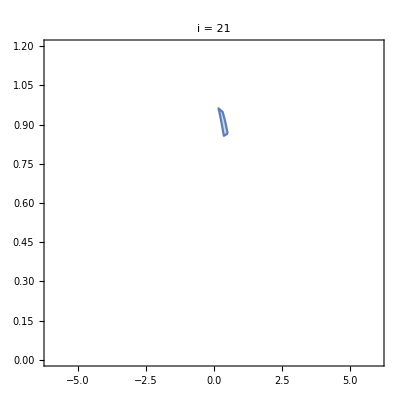
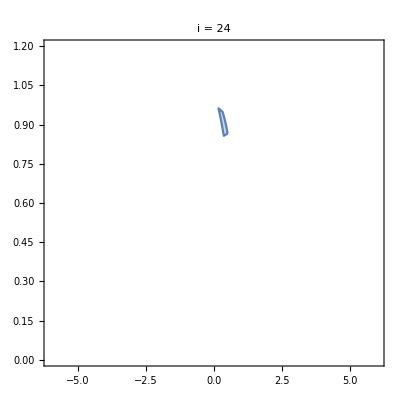
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}
]
```

```mathematica
is={10,11,18,19}
```

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
(1-k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)-(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)

```mathematica
Solve[λ[[1]]==0,e]
```

{{e→-1},{e→1}}

```mathematica
Solve[λ[[2]]==0,e]
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
Solve[λ[[3]]==0,e]
```

$Aborted

```mathematica
FullSimplify[(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2),Assumptions->k>0]
```

(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)

```mathematica
FullSimplify[k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k]
```

```mathematica
k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k
```

```mathematica
temp=FullSimplify[Numerator[Together[λ[[3]]]]]
```

-√(1-√(1-4 e^2 k^2))+k^2 √(1-√(1-4 e^2 k^2))-√(1-4 e^2 k^2) √(1-√(1-4 e^2 k^2))-2 e k √(1+√(1-4 e^2 k^2))-√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator//FullSimplify]
]
```

```mathematica
temp1=removeSqRoot[temp,√(1-√(1-4 e^2 k^2))]
```

4 k (-2 e^2 k^3+k (1-√(1-4 e^2 k^2)+2 e^2 √(1-4 e^2 k^2))+e √(1+√(1-4 e^2 k^2)) √(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))

```mathematica
temp2=removeSqRoot[temp1,√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))]
```

2 k^2 (1+8 e^6 k^2-√(1-4 e^2 k^2)+2 e^2 (-1+√(1-4 e^2 k^2)+k^2 (-2+√(1-4 e^2 k^2)))+e^4 (-2-4 √(1-4 e^2 k^2)+4 k^2 (2+√(1-4 e^2 k^2))))

```mathematica
temp3=removeSqRoot[temp2,√(1-4 e^2 k^2)]
```

4 e^4 (-1+2 e k) (1+2 e k) (-1+e^2+k^2) (3 (-1+e^2)+(k+2 e^2 k)^2)

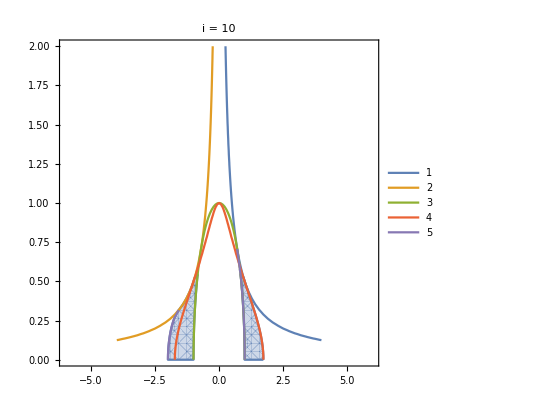

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];

p2=ContourPlot[{
-1+2 e k==0,
1+2 e k==0,
-1+e^2+k^2==0,
3 (-1+e^2)+(k+2 e^2 k)^2==0,
(1-k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k==0
},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,5}]];

Show[{p1,p2}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

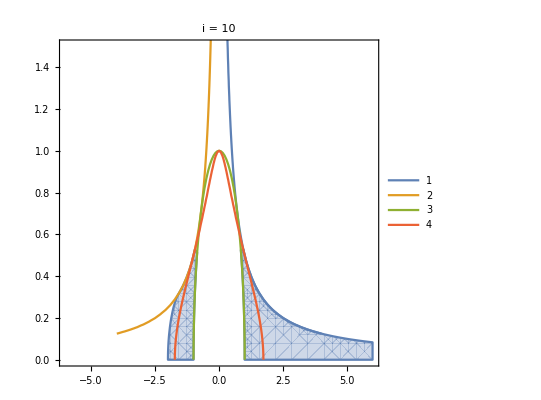

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]≤0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];

p2=ContourPlot[{
-1+2 e k==0,
1+2 e k==0,
-1+e^2+k^2==0,
3 (-1+e^2)+(k+2 e^2 k)^2==0
},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,4}]];

Show[{p1,p2}]
```

```mathematica
Solve[3 (-1+e^2)+(k+2 e^2 k)^2==0,e]
```

{{e→-(√(-4-3/k^2-(3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-4-3/k^2-(3 √(1+8 k^2))/k^2))/(2 √2)},{e→-(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2)}}

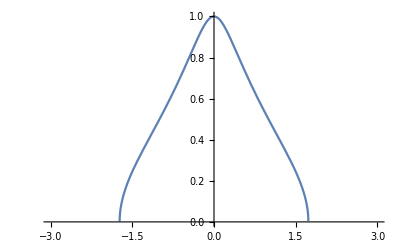

```mathematica
Plot[(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2),{k,-3,3}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

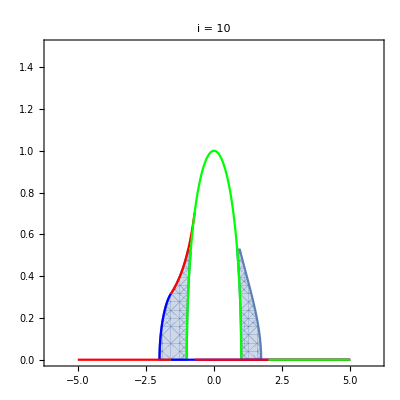

```mathematica
i=10;
k1=-√(5/2);
k2=-1/(√2);
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{Piecewise[{{-(√(-4+5 k^2-k^4))/(3 k), k≤k1}, {0, True}}],Piecewise[{{-1/(2k), k1≤k≤k3}, {0, True}}],Piecewise[{{√(1-k^2), k≤2}, {0, True}}]},{k,-5,5},PlotStyle->{Blue,Red,Green}];
Show[{p1,p2}]
```

Ok good.

#### Order parameter

```mathematica
i=10;
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

-(e (e-ⅈ √(1-e^2)) (-1+2 ⅈ √(e^2 k^2)+√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2))
(√2 e ⅇ^(-ⅈ (ArcCsc[(√2)/(√(1-√(1-4 e^2 k^2)))]-ArcSin[e])))/(√(1-√(1-4 e^2 k^2)))

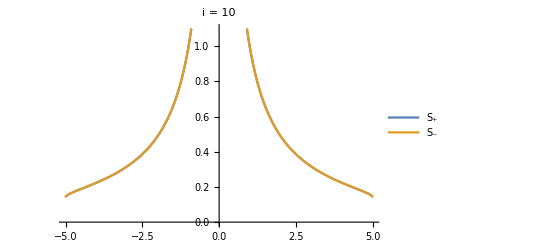
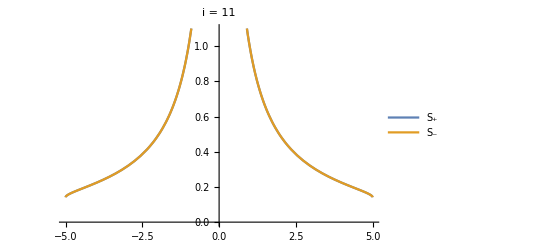
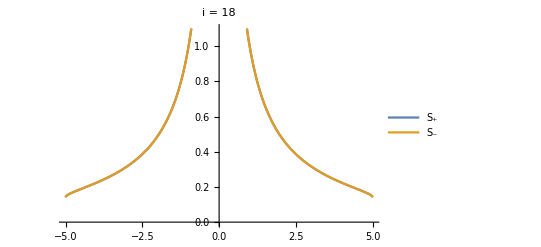
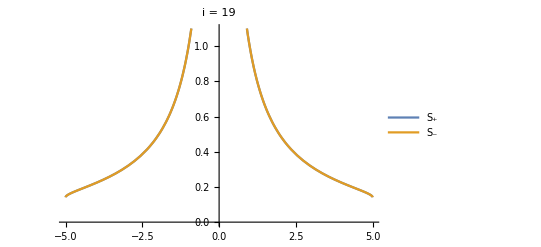

```mathematica
$Assumptions={};
ParallelTable[
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
kc=√(1-e^2)/.e->0.1;
Plot[{Abs[Wp2],Abs[Wm2]}/.e->0.1//Evaluate,{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,{10,11,18,19}}
]
```

### Fixed point 3

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,3]],etemp[[2,1]]}//FullSimplify;
TableForm[e3]
fp3=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp3]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]}}

32

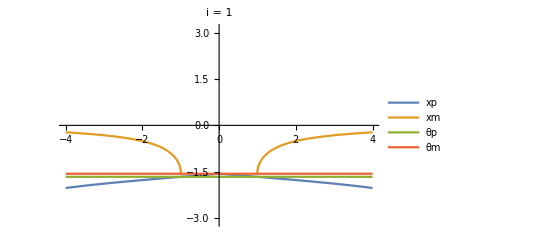
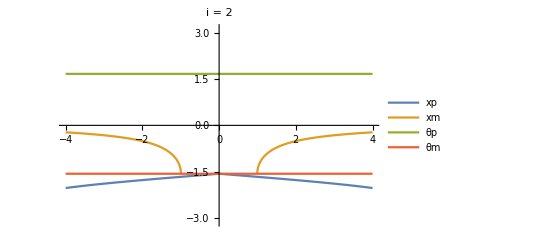
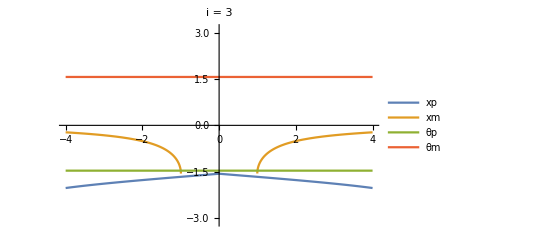
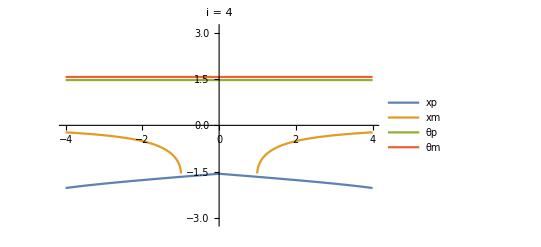
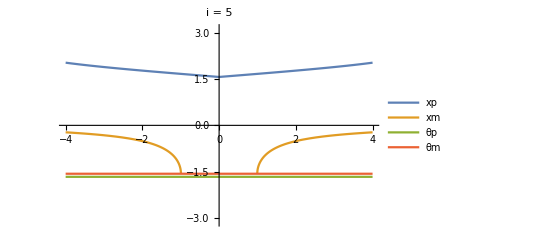
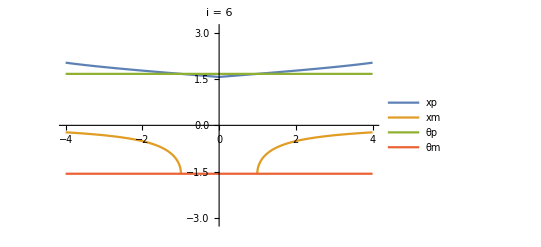
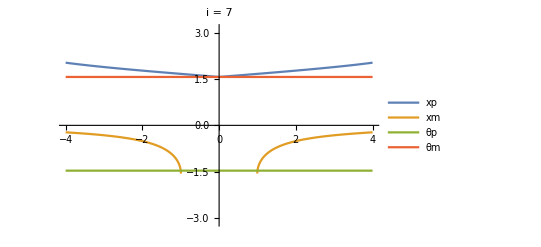
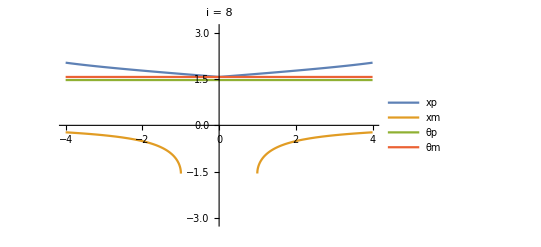

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp3[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp3]}
]
```

#### Eigenvalues

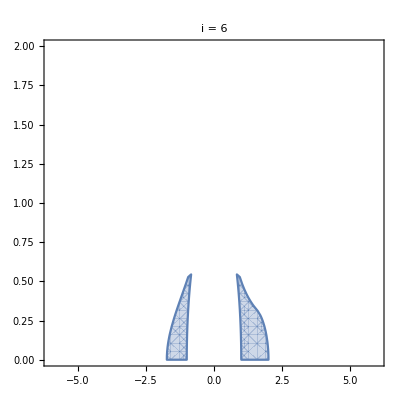
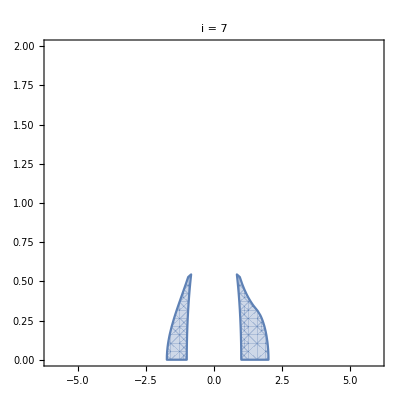
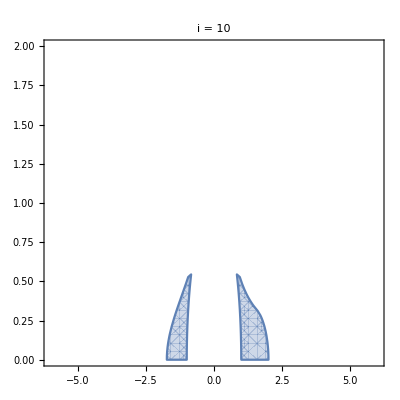
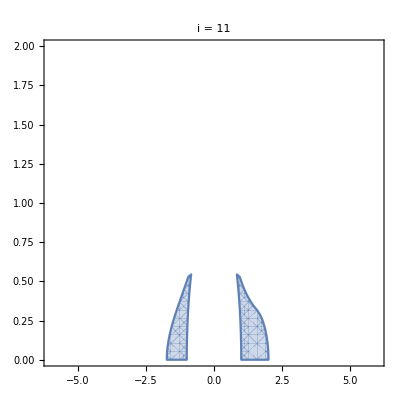
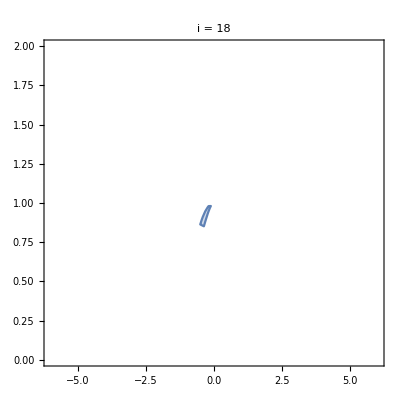
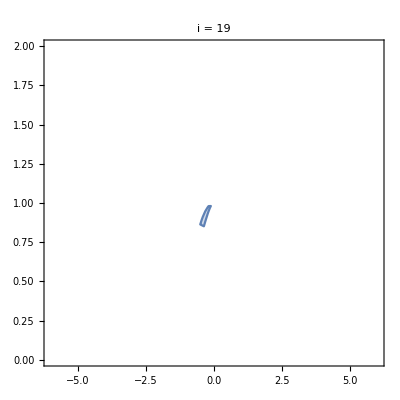
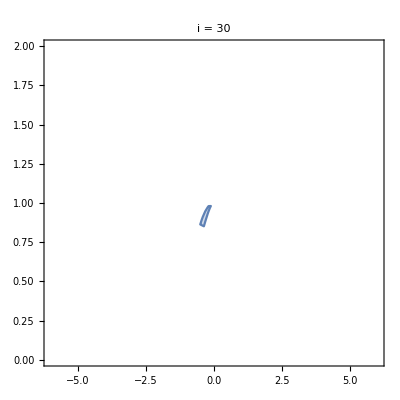
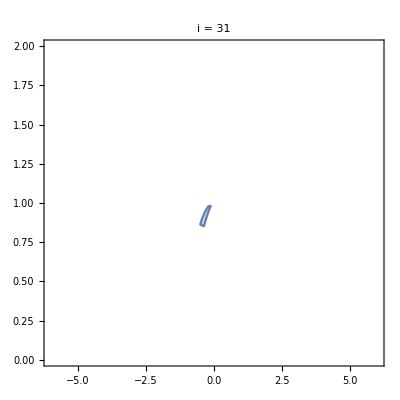
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp3[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp3[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp3]}
]
```

```mathematica
is={6,7}
```

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

√(1-e^2)
(-1+k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k
-(1-√(1-4 e^2 k^2)+(-k (2 e √(1-√(1-4 e^2 k^2))+k √(1+√(1-4 e^2 k^2)))+√(k^2 (4+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 (1-16 e^2+√(1-4 e^2 k^2)))))/(√(1+√(1-4 e^2 k^2))))/(2 k)
1/2 (k+(2 e √(1-√(1-4 e^2 k^2)))/(√(1+√(1-4 e^2 k^2)))+(-1+√(1-4 e^2 k^2)+(√(k^2 (4+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 (1-16 e^2+√(1-4 e^2 k^2)))))/(√(1+√(1-4 e^2 k^2))))/k)

```mathematica
Solve[-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
λ[[2]]
```

-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k

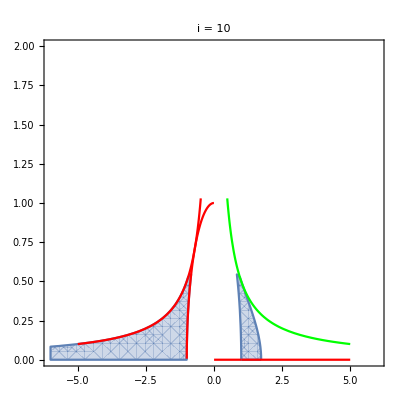

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{-1/(2k),√(1-k^2)HeavisideTheta[-k],1/(2k)},{k,-5,5},PlotStyle->{Red,Red,Green}];
Show[{p1,p2}]
```

#### Order parameter

```mathematica
is={6,7,10,11,18,19}
```

{6,7,10,11,18,19}

```mathematica
i=19;
Wp3=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wm3=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

-(e (e-ⅈ √(1-e^2)) (-1+2 ⅈ √(e^2 k^2)+√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2))
(√2 e ⅇ^(-ⅈ (ArcCsc[(√2)/(√(1-√(1-4 e^2 k^2)))]-ArcSin[e])))/(√(1-√(1-4 e^2 k^2)))

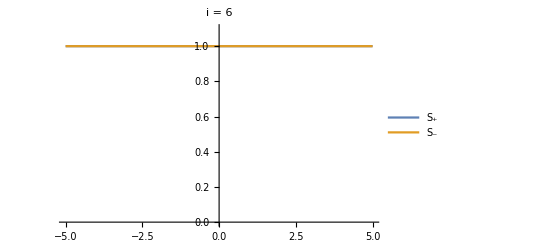
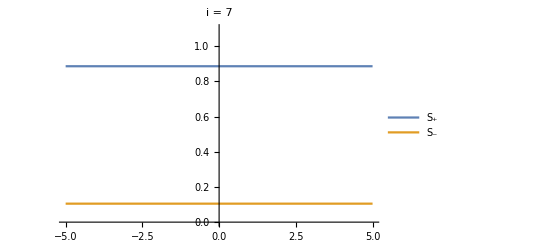

```mathematica
$Assumptions={};
ParallelTable[
Wp3=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wm3=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Plot[{Abs[Wp3],Abs[Wm3]}/.e->e1//Evaluate,{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,{6,7}}
]
```

```mathematica
$Assumptions={0≤e≤1,k∈Reals};
Abs[Wp3]//ComplexExpand//FullSimplify
```

Piecewise[{{(√2 e)/(√(1-√(1-4 e^2 k^2))), 4 e^2 k^2≤1}, {e/(√(e k (2 e k+√(-1+4 e^2 k^2)))), k<0&&4 e^2 k^2>1}, {√((e (2 e k+√(-1+4 e^2 k^2)))/k), True}}]

### Fixed point 4

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e4={etemp[[1,3]],etemp[[2,2]]}//FullSimplify;
TableForm[e4]
fp4=Solve[e4==0,{xp,θp}]//FullSimplify
Length[fp4]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

#### FP solve by hand

```mathematica
et1=e4[[1]]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]

```mathematica
Solve[et1==0,Sec[θp]]
```

{{Sec[θp]→-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)},{Sec[θp]→(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)}}

I’ve worked out sin θ=1/(√(1-1/(sec^2 θ)))

```mathematica
sub={Sec[θp]->(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k),Sin[θp]->√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)};
```

```mathematica
et2=FullSimplify[Numerator[Together[e4[[2]]/.sub]]]
```

-√k √(2 e k-Sin[2 xp])+2 e^2 √k Sec[xp]^2 √(2 e k-Sin[2 xp])-2 √e √(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator]
]
```

```mathematica
et3=removeSqRoot[et2,√(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))]//TrigExpand
```

-k/8+(e^2 k^3)/2-1/8 k Cos[xp]^2+1/2 e^2 k Cos[xp]^2-1/32 k Cos[xp]^4+1/8 k Sec[xp]^2-9/2 e^2 k Sec[xp]^2+8 e^4 k Sec[xp]^2+2 e^2 k^3 Sec[xp]^2-8 e^4 k^3 Sec[xp]^2+5/32 k Sec[xp]^4-4 e^2 k Sec[xp]^4+8 e^4 k Sec[xp]^4+3/2 e^2 k^3 Sec[xp]^4-8 e^4 k^3 Sec[xp]^4+16 e^6 k^3 Sec[xp]^4+3/2 e Cos[xp] Sin[xp]-3/2 e k^2 Cos[xp] Sin[xp]+15/8 k Sin[xp]^2-15/2 e^2 k Sin[xp]^2+7/8 k Cos[xp]^2 Sin[xp]^2-35/16 k Sin[xp]^4+4 e Tan[xp]-4 e k^2 Tan[xp]+16 e^3 k^2 Tan[xp]+5/2 e Sec[xp]^2 Tan[xp]-5/2 e k^2 Sec[xp]^2 Tan[xp]+16 e^3 k^2 Sec[xp]^2 Tan[xp]-32 e^5 k^2 Sec[xp]^2 Tan[xp]-5 e Sin[xp]^2 Tan[xp]+5 e k^2 Sin[xp]^2 Tan[xp]+3/4 k Tan[xp]^2-3 e^2 k^3 Tan[xp]^2-1/8 k Sec[xp]^2 Tan[xp]^2+9/2 e^2 k Sec[xp]^2 Tan[xp]^2-8 e^4 k Sec[xp]^2 Tan[xp]^2-2 e^2 k^3 Sec[xp]^2 Tan[xp]^2+8 e^4 k^3 Sec[xp]^2 Tan[xp]^2-15/8 k Sin[xp]^2 Tan[xp]^2+15/2 e^2 k Sin[xp]^2 Tan[xp]^2+7/8 k Sin[xp]^4 Tan[xp]^2-4 e Tan[xp]^3+4 e k^2 Tan[xp]^3-16 e^3 k^2 Tan[xp]^3+3/2 e Sin[xp]^2 Tan[xp]^3-3/2 e k^2 Sin[xp]^2 Tan[xp]^3-1/8 k Tan[xp]^4+1/2 e^2 k^3 Tan[xp]^4+1/8 k Sin[xp]^2 Tan[xp]^4-1/2 e^2 k Sin[xp]^2 Tan[xp]^4-1/32 k Sin[xp]^4 Tan[xp]^4

```mathematica
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(√(1-c^2))/c,Sin[xp]->√(1-c^2)};
et4=FullSimplify[Numerator[et3/.sub2//Simplify]][[2]]//FullSimplify
```

c^8 k-8 c^3 √(1-c^2) e^3 k^2+8 c √(1-c^2) e^5 k^2-4 e^6 k^3-c^6 (k+4 e^2 k)-c^4 e^2 k (-6+k^2)+2 c^5 √(1-c^2) e (-1+k^2)+4 c^2 e^4 k (-1+k^2)

```mathematica
et5=removeSqRoot[et4,√(1-c^2)]//FullSimplify
```

(c^6 (-1+c^2)+e^2 (c^2-2 e^2)^2 k^2) (4 c^4 e^2+c^2 (c^6-8 e^4-c^4 (1+8 e^2)+4 c^2 (e^2+4 e^4)) k^2+e^2 (c^2-2 e^2)^2 k^4)

I think these are clean polynomials in c^2....

```mathematica
et6=et5/.c->√c1//FullSimplify
```

((-1+c1) c1^3+e^2 (c1-2 e^2)^2 k^2) (4 c1^2 e^2+c1 ((-1+c1) c1^2+4 (1-2 c1) c1 e^2+8 (-1+2 c1) e^4) k^2+e^2 (c1-2 e^2)^2 k^4)

```mathematica
Collect[et6[[1]],c1]
```

-c1^3+c1^4+c1^2 e^2 k^2-4 c1 e^4 k^2+4 e^6 k^2

```mathematica
Collect[et6[[2]],c1]
```

c1^4 k^2+4 e^6 k^4+c1^3 (-k^2-8 e^2 k^2)+c1^2 (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)+c1 (-8 e^4 k^2-4 e^4 k^4)

Yes, a cubic and a quartic in c1 = c^2. So they have known, but ugly, solutions. Nice!! In principle I’m done. Just gotta fold back

```mathematica
Collect[et4,k]
```

-2 c^5 √(1-c^2) e+(-c^6+c^8+6 c^4 e^2-4 c^6 e^2-4 c^2 e^4) k+(2 c^5 √(1-c^2) e-8 c^3 √(1-c^2) e^3+8 c √(1-c^2) e^5) k^2+(-c^4 e^2+4 c^2 e^4-4 e^6) k^3

```mathematica
fp4sub=Solve[et5==0,c];
Length[fp4sub]
fp4sub
```

16

{{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))}}

#### Collect

```mathematica
Clear[k,e]
fp4=Table[{xp->ArcCos[c],xm->ArcSin[e Sec[xp]]/.xp->ArcCos[c],θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))],θm->ArcSin[e Sec[θp]]/.θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))]}/.fp4sub[[i]],{i,1,Length[fp4sub]}];
```

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

```mathematica
i=8;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

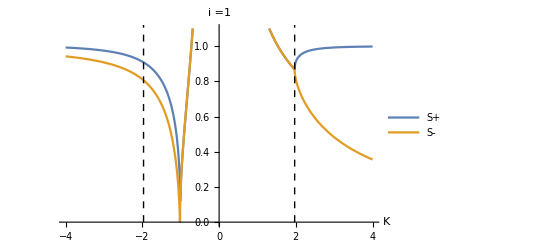
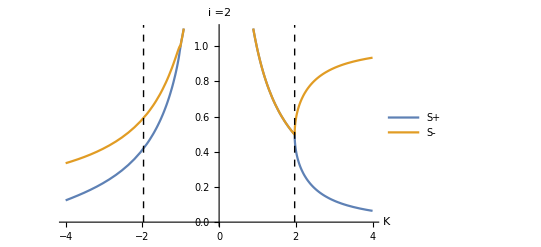
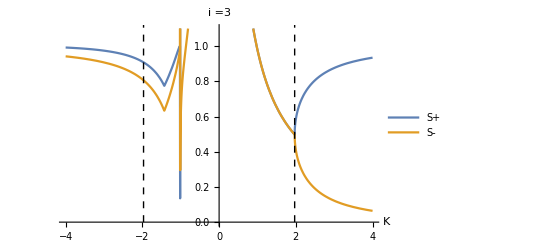
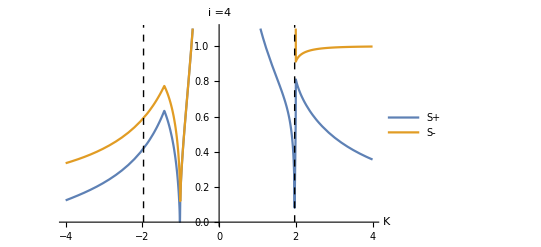
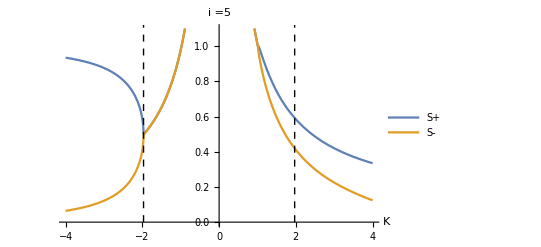
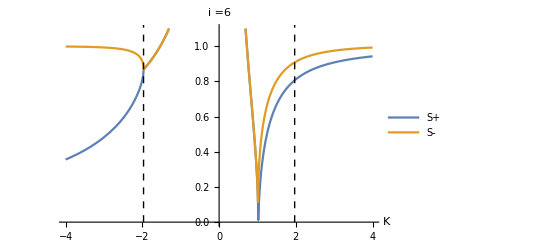
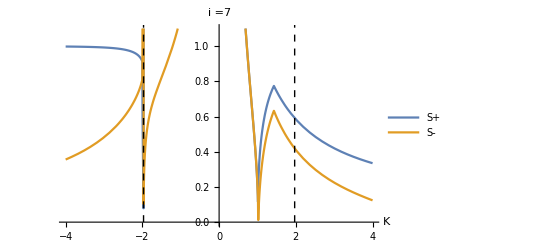
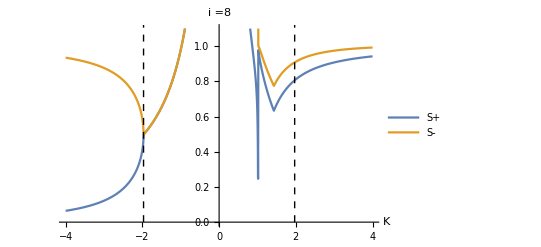
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

Plot versus E

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.k->3],Abs[Wm4/.k->3]},{e,0,5},PlotRange->{0,1.1},AxesLabel->{"E"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
```

```mathematica
$Assumptions={{e,k}∈Reals};
ComplexExpand[Abs[Wp4],TargetFunctions->{Re, Im}]
```

√((1)^2+((e^2 Cos[1/2 ArcTan[1]] Cos[1/2 ArcTan[1/4+3+1/2 Cos[1/2 1] (1)^(1/4),1]] ((1)^2+(1)^2)^(1/4))/(((1/4+3+1)^2+(1)^2)^(1/4))+1/1+10+1+(1^2/(4 e^2 k^2)+(1-1)^2)^(1/4) Sin[1/2 ArcTan[1-1/(2 e k),-1/(2 e k)]] (1))^2)
 |  |  |  |

```mathematica
p2=ContourPlot[2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2==0,{k,-4,4},{e,0,1.5}]
```

-Graphics-

```mathematica
p3=Plot[1/2 √(1-1/k^2+(√(-4+k^2))/k),{k,-4,4}];
Show[{pfinal,p3}]
```

-Graphics-

#### Plot

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.fp4[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp4]}
]
```

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.44246×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.901507+1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507+5.52014×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcSin[0.808364-4.9498×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507-1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Eigenvalues

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.fp4[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.fp4[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-4,3},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,2}
]
```

$Aborted

```mathematica
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
J1=J/.fp4[[i]];
λ=Eigenvalues[J1];
TableForm[λ]
```

$Aborted

Root[2 k Cos[xm-xp]-2 k Cos[3 xm-xp]-2 k Cos[xm+xp]+2 k Cos[3 xm+xp]+k Cos[xm-xp-4 θm]-k Cos[3 xm-xp-4 θm]-k Cos[xm+xp-4 θm]+k Cos[3 xm+xp-4 θm]+4 Cos[2 xm-2 θm]+4 Cos[2 xp-2 θm]+4 Cos[2 xm+2 θm]+4 Cos[2 xp+2 θm]+k Cos[xm-xp+4 θm]-k Cos[3 xm-xp+4 θm]-k Cos[xm+xp+4 θm]+k Cos[3 xm+xp+4 θm]+4 Cos[2 xm-2 θp]+4 Cos[2 xp-2 θp]+k Cos[xm-xp-2 θm-2 θp]-k Cos[3 xm-xp-2 θm-2 θp]-k Cos[xm+xp-2 θm-2 θp]+k Cos[3 xm+xp-2 θm-2 θp]+k Cos[xm-xp+2 θm-2 θp]-k Cos[3 xm-xp+2 θm-2 θp]-k Cos[xm+xp+2 θm-2 θp]+k Cos[3 xm+xp+2 θm-2 θp]+k^2 Cos[xm-xp-5 θm-θp]-k^2 Cos[xm+xp-5 θm-θp]-k Cos[4 xm-3 θm-θp]-k Cos[2 xm-2 xp-3 θm-θp]-k^2 Cos[xm-xp-3 θm-θp]+k^2 Cos[xm+xp-3 θm-θp]-k Cos[2 xm+2 xp-3 θm-θp]+k Cos[4 xm-θm-θp]+k Cos[2 xm-2 xp-θm-θp]-k^2 Cos[3 xm-xp-θm-θp]+k^2 Cos[5 xm-xp-θm-θp]+k^2 Cos[3 xm+xp-θm-θp]-k^2 Cos[5 xm+xp-θm-θp]+k Cos[2 xm+2 xp-θm-θp]-2 k Cos[θm-θp]-k Cos[4 xm+θm-θp]-k Cos[2 xm-2 xp+θm-θp]+k^2 Cos[3 xm-xp+θm-θp]-k^2 Cos[5 xm-xp+θm-θp]-k^2 Cos[3 xm+xp+θm-θp]+k^2 Cos[5 xm+xp+θm-θp]-k Cos[2 xm+2 xp+θm-θp]+2 k Cos[3 θm-θp]+k Cos[4 xm+3 θm-θp]+k Cos[2 xm-2 xp+3 θm-θp]+k^2 Cos[xm-xp+3 θm-θp]-k^2 Cos[xm+xp+3 θm-θp]+k Cos[2 xm+2 xp+3 θm-θp]-k^2 Cos[xm-xp+5 θm-θp]+k^2 Cos[xm+xp+5 θm-θp]-k^2 Cos[xm-xp-5 θm+θp]+k^2 Cos[xm+xp-5 θm+θp]+k Cos[4 xm-3 θm+θp]+k Cos[2 xm-2 xp-3 θm+θp]+k^2 Cos[xm-xp-3 θm+θp]-k^2 Cos[xm+xp-3 θm+θp]+k Cos[2 xm+2 xp-3 θm+θp]-k Cos[4 xm-θm+θp]-k Cos[2 xm-2 xp-θm+θp]+k^2 Cos[3 xm-xp-θm+θp]-k^2 Cos[5 xm-xp-θm+θp]-k^2 Cos[3 xm+xp-θm+θp]+k^2 Cos[5 xm+xp-θm+θp]-k Cos[2 xm+2 xp-θm+θp]+2 k Cos[θm+θp]+k Cos[4 xm+θm+θp]+k Cos[2 xm-2 xp+θm+θp]-k^2 Cos[3 xm-xp+θm+θp]+k^2 Cos[5 xm-xp+θm+θp]+k^2 Cos[3 xm+xp+θm+θp]-k^2 Cos[5 xm+xp+θm+θp]+k Cos[2 xm+2 xp+θm+θp]-2 k Cos[3 θm+θp]-k Cos[4 xm+3 θm+θp]-k Cos[2 xm-2 xp+3 θm+θp]-k^2 Cos[xm-xp+3 θm+θp]+k^2 Cos[xm+xp+3 θm+θp]-k Cos[2 xm+2 xp+3 θm+θp]+k^2 Cos[xm-xp+5 θm+θp]-k^2 Cos[xm+xp+5 θm+θp]+4 Cos[2 xm+2 θp]+4 Cos[2 xp+2 θp]+k Cos[xm-xp-2 θm+2 θp]-k Cos[3 xm-xp-2 θm+2 θp]-k Cos[xm+xp-2 θm+2 θp]+k Cos[3 xm+xp-2 θm+2 θp]+k Cos[xm-xp+2 θm+2 θp]-k Cos[3 xm-xp+2 θm+2 θp]-k Cos[xm+xp+2 θm+2 θp]+k Cos[3 xm+xp+2 θm+2 θp]+(8 k Cos[2 xm]-4 k^2 Cos[3 xm-xp]+4 k^2 Cos[5 xm-xp]+4 k^2 Cos[3 xm+xp]-4 k^2 Cos[5 xm+xp]+4 k Cos[2 xm-4 θm]+4 k^2 Cos[xm-xp-4 θm]-4 k^2 Cos[xm+xp-4 θm]-4 k Cos[4 xm-2 θm]-4 k Cos[2 xm-2 xp-2 θm]+8 Cos[xm-xp-2 θm]-8 Cos[xm+xp-2 θm]-4 k Cos[2 xm+2 xp-2 θm]-8 k Cos[2 θm]-4 k Cos[4 xm+2 θm]-4 k Cos[2 xm-2 xp+2 θm]+8 Cos[xm-xp+2 θm]-8 Cos[xm+xp+2 θm]-4 k Cos[2 xm+2 xp+2 θm]+4 k Cos[2 xm+4 θm]+4 k^2 Cos[xm-xp+4 θm]-4 k^2 Cos[xm+xp+4 θm]+8 Cos[xm-xp-2 θp]-8 Cos[xm+xp-2 θp]+4 k Cos[2 xm-2 θm-2 θp]+4 k Cos[2 xm+2 θm-2 θp]-8 Cos[2 xm-θm-θp]-4 k^2 Cos[4 xm-θm-θp]-8 Cos[2 xp-θm-θp]+8 Cos[2 xm+θm-θp]+4 k^2 Cos[4 xm+θm-θp]+8 Cos[2 xp+θm-θp]-4 k^2 Cos[3 θm-θp]+4 k^2 Cos[5 θm-θp]+8 Cos[2 xm-θm+θp]+4 k^2 Cos[4 xm-θm+θp]+8 Cos[2 xp-θm+θp]-8 Cos[2 xm+θm+θp]-4 k^2 Cos[4 xm+θm+θp]-8 Cos[2 xp+θm+θp]+4 k^2 Cos[3 θm+θp]-4 k^2 Cos[5 θm+θp]+8 Cos[xm-xp+2 θp]-8 Cos[xm+xp+2 θp]+4 k Cos[2 xm-2 θm+2 θp]+4 k Cos[2 xm+2 θm+2 θp]) #1+(-16 Cos[2 xm]-16 k^2 Cos[4 xm]-16 Cos[2 xp]+4 k Cos[xm-xp-2 θm]-4 k Cos[3 xm-xp-2 θm]-4 k Cos[xm+xp-2 θm]+4 k Cos[3 xm+xp-2 θm]-16 Cos[2 θm]-16 k^2 Cos[4 θm]+4 k Cos[xm-xp+2 θm]-4 k Cos[3 xm-xp+2 θm]-4 k Cos[xm+xp+2 θm]+4 k Cos[3 xm+xp+2 θm]-4 k Cos[2 xm-3 θm-θp]+4 k Cos[2 xm-θm-θp]-16 Cos[xm-xp-θm-θp]+16 Cos[xm+xp-θm-θp]-4 k Cos[2 xm+θm-θp]+16 Cos[xm-xp+θm-θp]-16 Cos[xm+xp+θm-θp]+4 k Cos[2 xm+3 θm-θp]-16 Cos[2 θp]+4 k Cos[2 xm-3 θm+θp]-4 k Cos[2 xm-θm+θp]+16 Cos[xm-xp-θm+θp]-16 Cos[xm+xp-θm+θp]+4 k Cos[2 xm+θm+θp]-16 Cos[xm-xp+θm+θp]+16 Cos[xm+xp+θm+θp]-4 k Cos[2 xm+3 θm+θp]) #1^2+(-32 Cos[xm-xp]+32 Cos[xm+xp]-32 Cos[θm-θp]+32 Cos[θm+θp]) #1^3+32 #1^4&,1]
Root[2 k Cos[xm-xp]-2 k Cos[3 xm-xp]-2 k Cos[xm+xp]+2 k Cos[3 xm+xp]+k Cos[xm-xp-4 θm]-k Cos[3 xm-xp-4 θm]-k Cos[xm+xp-4 θm]+k Cos[3 xm+xp-4 θm]+4 Cos[2 xm-2 θm]+4 Cos[2 xp-2 θm]+4 Cos[2 xm+2 θm]+4 Cos[2 xp+2 θm]+k Cos[xm-xp+4 θm]-k Cos[3 xm-xp+4 θm]-k Cos[xm+xp+4 θm]+k Cos[3 xm+xp+4 θm]+4 Cos[2 xm-2 θp]+4 Cos[2 xp-2 θp]+k Cos[xm-xp-2 θm-2 θp]-k Cos[3 xm-xp-2 θm-2 θp]-k Cos[xm+xp-2 θm-2 θp]+k Cos[3 xm+xp-2 θm-2 θp]+k Cos[xm-xp+2 θm-2 θp]-k Cos[3 xm-xp+2 θm-2 θp]-k Cos[xm+xp+2 θm-2 θp]+k Cos[3 xm+xp+2 θm-2 θp]+k^2 Cos[xm-xp-5 θm-θp]-k^2 Cos[xm+xp-5 θm-θp]-k Cos[4 xm-3 θm-θp]-k Cos[2 xm-2 xp-3 θm-θp]-k^2 Cos[xm-xp-3 θm-θp]+k^2 Cos[xm+xp-3 θm-θp]-k Cos[2 xm+2 xp-3 θm-θp]+k Cos[4 xm-θm-θp]+k Cos[2 xm-2 xp-θm-θp]-k^2 Cos[3 xm-xp-θm-θp]+k^2 Cos[5 xm-xp-θm-θp]+k^2 Cos[3 xm+xp-θm-θp]-k^2 Cos[5 xm+xp-θm-θp]+k Cos[2 xm+2 xp-θm-θp]-2 k Cos[θm-θp]-k Cos[4 xm+θm-θp]-k Cos[2 xm-2 xp+θm-θp]+k^2 Cos[3 xm-xp+θm-θp]-k^2 Cos[5 xm-xp+θm-θp]-k^2 Cos[3 xm+xp+θm-θp]+k^2 Cos[5 xm+xp+θm-θp]-k Cos[2 xm+2 xp+θm-θp]+2 k Cos[3 θm-θp]+k Cos[4 xm+3 θm-θp]+k Cos[2 xm-2 xp+3 θm-θp]+k^2 Cos[xm-xp+3 θm-θp]-k^2 Cos[xm+xp+3 θm-θp]+k Cos[2 xm+2 xp+3 θm-θp]-k^2 Cos[xm-xp+5 θm-θp]+k^2 Cos[xm+xp+5 θm-θp]-k^2 Cos[xm-xp-5 θm+θp]+k^2 Cos[xm+xp-5 θm+θp]+k Cos[4 xm-3 θm+θp]+k Cos[2 xm-2 xp-3 θm+θp]+k^2 Cos[xm-xp-3 θm+θp]-k^2 Cos[xm+xp-3 θm+θp]+k Cos[2 xm+2 xp-3 θm+θp]-k Cos[4 xm-θm+θp]-k Cos[2 xm-2 xp-θm+θp]+k^2 Cos[3 xm-xp-θm+θp]-k^2 Cos[5 xm-xp-θm+θp]-k^2 Cos[3 xm+xp-θm+θp]+k^2 Cos[5 xm+xp-θm+θp]-k Cos[2 xm+2 xp-θm+θp]+2 k Cos[θm+θp]+k Cos[4 xm+θm+θp]+k Cos[2 xm-2 xp+θm+θp]-k^2 Cos[3 xm-xp+θm+θp]+k^2 Cos[5 xm-xp+θm+θp]+k^2 Cos[3 xm+xp+θm+θp]-k^2 Cos[5 xm+xp+θm+θp]+k Cos[2 xm+2 xp+θm+θp]-2 k Cos[3 θm+θp]-k Cos[4 xm+3 θm+θp]-k Cos[2 xm-2 xp+3 θm+θp]-k^2 Cos[xm-xp+3 θm+θp]+k^2 Cos[xm+xp+3 θm+θp]-k Cos[2 xm+2 xp+3 θm+θp]+k^2 Cos[xm-xp+5 θm+θp]-k^2 Cos[xm+xp+5 θm+θp]+4 Cos[2 xm+2 θp]+4 Cos[2 xp+2 θp]+k Cos[xm-xp-2 θm+2 θp]-k Cos[3 xm-xp-2 θm+2 θp]-k Cos[xm+xp-2 θm+2 θp]+k Cos[3 xm+xp-2 θm+2 θp]+k Cos[xm-xp+2 θm+2 θp]-k Cos[3 xm-xp+2 θm+2 θp]-k Cos[xm+xp+2 θm+2 θp]+k Cos[3 xm+xp+2 θm+2 θp]+(8 k Cos[2 xm]-4 k^2 Cos[3 xm-xp]+4 k^2 Cos[5 xm-xp]+4 k^2 Cos[3 xm+xp]-4 k^2 Cos[5 xm+xp]+4 k Cos[2 xm-4 θm]+4 k^2 Cos[xm-xp-4 θm]-4 k^2 Cos[xm+xp-4 θm]-4 k Cos[4 xm-2 θm]-4 k Cos[2 xm-2 xp-2 θm]+8 Cos[xm-xp-2 θm]-8 Cos[xm+xp-2 θm]-4 k Cos[2 xm+2 xp-2 θm]-8 k Cos[2 θm]-4 k Cos[4 xm+2 θm]-4 k Cos[2 xm-2 xp+2 θm]+8 Cos[xm-xp+2 θm]-8 Cos[xm+xp+2 θm]-4 k Cos[2 xm+2 xp+2 θm]+4 k Cos[2 xm+4 θm]+4 k^2 Cos[xm-xp+4 θm]-4 k^2 Cos[xm+xp+4 θm]+8 Cos[xm-xp-2 θp]-8 Cos[xm+xp-2 θp]+4 k Cos[2 xm-2 θm-2 θp]+4 k Cos[2 xm+2 θm-2 θp]-8 Cos[2 xm-θm-θp]-4 k^2 Cos[4 xm-θm-θp]-8 Cos[2 xp-θm-θp]+8 Cos[2 xm+θm-θp]+4 k^2 Cos[4 xm+θm-θp]+8 Cos[2 xp+θm-θp]-4 k^2 Cos[3 θm-θp]+4 k^2 Cos[5 θm-θp]+8 Cos[2 xm-θm+θp]+4 k^2 Cos[4 xm-θm+θp]+8 Cos[2 xp-θm+θp]-8 Cos[2 xm+θm+θp]-4 k^2 Cos[4 xm+θm+θp]-8 Cos[2 xp+θm+θp]+4 k^2 Cos[3 θm+θp]-4 k^2 Cos[5 θm+θp]+8 Cos[xm-xp+2 θp]-8 Cos[xm+xp+2 θp]+4 k Cos[2 xm-2 θm+2 θp]+4 k Cos[2 xm+2 θm+2 θp]) #1+(-16 Cos[2 xm]-16 k^2 Cos[4 xm]-16 Cos[2 xp]+4 k Cos[xm-xp-2 θm]-4 k Cos[3 xm-xp-2 θm]-4 k Cos[xm+xp-2 θm]+4 k Cos[3 xm+xp-2 θm]-16 Cos[2 θm]-16 k^2 Cos[4 θm]+4 k Cos[xm-xp+2 θm]-4 k Cos[3 xm-xp+2 θm]-4 k Cos[xm+xp+2 θm]+4 k Cos[3 xm+xp+2 θm]-4 k Cos[2 xm-3 θm-θp]+4 k Cos[2 xm-θm-θp]-16 Cos[xm-xp-θm-θp]+16 Cos[xm+xp-θm-θp]-4 k Cos[2 xm+θm-θp]+16 Cos[xm-xp+θm-θp]-16 Cos[xm+xp+θm-θp]+4 k Cos[2 xm+3 θm-θp]-16 Cos[2 θp]+4 k Cos[2 xm-3 θm+θp]-4 k Cos[2 xm-θm+θp]+16 Cos[xm-xp-θm+θp]-16 Cos[xm+xp-θm+θp]+4 k Cos[2 xm+θm+θp]-16 Cos[xm-xp+θm+θp]+16 Cos[xm+xp+θm+θp]-4 k Cos[2 xm+3 θm+θp]) #1^2+(-32 Cos[xm-xp]+32 Cos[xm+xp]-32 Cos[θm-θp]+32 Cos[θm+θp]) #1^3+32 #1^4&,2]
Root[2 k Cos[xm-xp]-2 k Cos[3 xm-xp]-2 k Cos[xm+xp]+2 k Cos[3 xm+xp]+k Cos[xm-xp-4 θm]-k Cos[3 xm-xp-4 θm]-k Cos[xm+xp-4 θm]+k Cos[3 xm+xp-4 θm]+4 Cos[2 xm-2 θm]+4 Cos[2 xp-2 θm]+4 Cos[2 xm+2 θm]+4 Cos[2 xp+2 θm]+k Cos[xm-xp+4 θm]-k Cos[3 xm-xp+4 θm]-k Cos[xm+xp+4 θm]+k Cos[3 xm+xp+4 θm]+4 Cos[2 xm-2 θp]+4 Cos[2 xp-2 θp]+k Cos[xm-xp-2 θm-2 θp]-k Cos[3 xm-xp-2 θm-2 θp]-k Cos[xm+xp-2 θm-2 θp]+k Cos[3 xm+xp-2 θm-2 θp]+k Cos[xm-xp+2 θm-2 θp]-k Cos[3 xm-xp+2 θm-2 θp]-k Cos[xm+xp+2 θm-2 θp]+k Cos[3 xm+xp+2 θm-2 θp]+k^2 Cos[xm-xp-5 θm-θp]-k^2 Cos[xm+xp-5 θm-θp]-k Cos[4 xm-3 θm-θp]-k Cos[2 xm-2 xp-3 θm-θp]-k^2 Cos[xm-xp-3 θm-θp]+k^2 Cos[xm+xp-3 θm-θp]-k Cos[2 xm+2 xp-3 θm-θp]+k Cos[4 xm-θm-θp]+k Cos[2 xm-2 xp-θm-θp]-k^2 Cos[3 xm-xp-θm-θp]+k^2 Cos[5 xm-xp-θm-θp]+k^2 Cos[3 xm+xp-θm-θp]-k^2 Cos[5 xm+xp-θm-θp]+k Cos[2 xm+2 xp-θm-θp]-2 k Cos[θm-θp]-k Cos[4 xm+θm-θp]-k Cos[2 xm-2 xp+θm-θp]+k^2 Cos[3 xm-xp+θm-θp]-k^2 Cos[5 xm-xp+θm-θp]-k^2 Cos[3 xm+xp+θm-θp]+k^2 Cos[5 xm+xp+θm-θp]-k Cos[2 xm+2 xp+θm-θp]+2 k Cos[3 θm-θp]+k Cos[4 xm+3 θm-θp]+k Cos[2 xm-2 xp+3 θm-θp]+k^2 Cos[xm-xp+3 θm-θp]-k^2 Cos[xm+xp+3 θm-θp]+k Cos[2 xm+2 xp+3 θm-θp]-k^2 Cos[xm-xp+5 θm-θp]+k^2 Cos[xm+xp+5 θm-θp]-k^2 Cos[xm-xp-5 θm+θp]+k^2 Cos[xm+xp-5 θm+θp]+k Cos[4 xm-3 θm+θp]+k Cos[2 xm-2 xp-3 θm+θp]+k^2 Cos[xm-xp-3 θm+θp]-k^2 Cos[xm+xp-3 θm+θp]+k Cos[2 xm+2 xp-3 θm+θp]-k Cos[4 xm-θm+θp]-k Cos[2 xm-2 xp-θm+θp]+k^2 Cos[3 xm-xp-θm+θp]-k^2 Cos[5 xm-xp-θm+θp]-k^2 Cos[3 xm+xp-θm+θp]+k^2 Cos[5 xm+xp-θm+θp]-k Cos[2 xm+2 xp-θm+θp]+2 k Cos[θm+θp]+k Cos[4 xm+θm+θp]+k Cos[2 xm-2 xp+θm+θp]-k^2 Cos[3 xm-xp+θm+θp]+k^2 Cos[5 xm-xp+θm+θp]+k^2 Cos[3 xm+xp+θm+θp]-k^2 Cos[5 xm+xp+θm+θp]+k Cos[2 xm+2 xp+θm+θp]-2 k Cos[3 θm+θp]-k Cos[4 xm+3 θm+θp]-k Cos[2 xm-2 xp+3 θm+θp]-k^2 Cos[xm-xp+3 θm+θp]+k^2 Cos[xm+xp+3 θm+θp]-k Cos[2 xm+2 xp+3 θm+θp]+k^2 Cos[xm-xp+5 θm+θp]-k^2 Cos[xm+xp+5 θm+θp]+4 Cos[2 xm+2 θp]+4 Cos[2 xp+2 θp]+k Cos[xm-xp-2 θm+2 θp]-k Cos[3 xm-xp-2 θm+2 θp]-k Cos[xm+xp-2 θm+2 θp]+k Cos[3 xm+xp-2 θm+2 θp]+k Cos[xm-xp+2 θm+2 θp]-k Cos[3 xm-xp+2 θm+2 θp]-k Cos[xm+xp+2 θm+2 θp]+k Cos[3 xm+xp+2 θm+2 θp]+(8 k Cos[2 xm]-4 k^2 Cos[3 xm-xp]+4 k^2 Cos[5 xm-xp]+4 k^2 Cos[3 xm+xp]-4 k^2 Cos[5 xm+xp]+4 k Cos[2 xm-4 θm]+4 k^2 Cos[xm-xp-4 θm]-4 k^2 Cos[xm+xp-4 θm]-4 k Cos[4 xm-2 θm]-4 k Cos[2 xm-2 xp-2 θm]+8 Cos[xm-xp-2 θm]-8 Cos[xm+xp-2 θm]-4 k Cos[2 xm+2 xp-2 θm]-8 k Cos[2 θm]-4 k Cos[4 xm+2 θm]-4 k Cos[2 xm-2 xp+2 θm]+8 Cos[xm-xp+2 θm]-8 Cos[xm+xp+2 θm]-4 k Cos[2 xm+2 xp+2 θm]+4 k Cos[2 xm+4 θm]+4 k^2 Cos[xm-xp+4 θm]-4 k^2 Cos[xm+xp+4 θm]+8 Cos[xm-xp-2 θp]-8 Cos[xm+xp-2 θp]+4 k Cos[2 xm-2 θm-2 θp]+4 k Cos[2 xm+2 θm-2 θp]-8 Cos[2 xm-θm-θp]-4 k^2 Cos[4 xm-θm-θp]-8 Cos[2 xp-θm-θp]+8 Cos[2 xm+θm-θp]+4 k^2 Cos[4 xm+θm-θp]+8 Cos[2 xp+θm-θp]-4 k^2 Cos[3 θm-θp]+4 k^2 Cos[5 θm-θp]+8 Cos[2 xm-θm+θp]+4 k^2 Cos[4 xm-θm+θp]+8 Cos[2 xp-θm+θp]-8 Cos[2 xm+θm+θp]-4 k^2 Cos[4 xm+θm+θp]-8 Cos[2 xp+θm+θp]+4 k^2 Cos[3 θm+θp]-4 k^2 Cos[5 θm+θp]+8 Cos[xm-xp+2 θp]-8 Cos[xm+xp+2 θp]+4 k Cos[2 xm-2 θm+2 θp]+4 k Cos[2 xm+2 θm+2 θp]) #1+(-16 Cos[2 xm]-16 k^2 Cos[4 xm]-16 Cos[2 xp]+4 k Cos[xm-xp-2 θm]-4 k Cos[3 xm-xp-2 θm]-4 k Cos[xm+xp-2 θm]+4 k Cos[3 xm+xp-2 θm]-16 Cos[2 θm]-16 k^2 Cos[4 θm]+4 k Cos[xm-xp+2 θm]-4 k Cos[3 xm-xp+2 θm]-4 k Cos[xm+xp+2 θm]+4 k Cos[3 xm+xp+2 θm]-4 k Cos[2 xm-3 θm-θp]+4 k Cos[2 xm-θm-θp]-16 Cos[xm-xp-θm-θp]+16 Cos[xm+xp-θm-θp]-4 k Cos[2 xm+θm-θp]+16 Cos[xm-xp+θm-θp]-16 Cos[xm+xp+θm-θp]+4 k Cos[2 xm+3 θm-θp]-16 Cos[2 θp]+4 k Cos[2 xm-3 θm+θp]-4 k Cos[2 xm-θm+θp]+16 Cos[xm-xp-θm+θp]-16 Cos[xm+xp-θm+θp]+4 k Cos[2 xm+θm+θp]-16 Cos[xm-xp+θm+θp]+16 Cos[xm+xp+θm+θp]-4 k Cos[2 xm+3 θm+θp]) #1^2+(-32 Cos[xm-xp]+32 Cos[xm+xp]-32 Cos[θm-θp]+32 Cos[θm+θp]) #1^3+32 #1^4&,3]
Root[2 k Cos[xm-xp]-2 k Cos[3 xm-xp]-2 k Cos[xm+xp]+2 k Cos[3 xm+xp]+k Cos[xm-xp-4 θm]-k Cos[3 xm-xp-4 θm]-k Cos[xm+xp-4 θm]+k Cos[3 xm+xp-4 θm]+4 Cos[2 xm-2 θm]+4 Cos[2 xp-2 θm]+4 Cos[2 xm+2 θm]+4 Cos[2 xp+2 θm]+k Cos[xm-xp+4 θm]-k Cos[3 xm-xp+4 θm]-k Cos[xm+xp+4 θm]+k Cos[3 xm+xp+4 θm]+4 Cos[2 xm-2 θp]+4 Cos[2 xp-2 θp]+k Cos[xm-xp-2 θm-2 θp]-k Cos[3 xm-xp-2 θm-2 θp]-k Cos[xm+xp-2 θm-2 θp]+k Cos[3 xm+xp-2 θm-2 θp]+k Cos[xm-xp+2 θm-2 θp]-k Cos[3 xm-xp+2 θm-2 θp]-k Cos[xm+xp+2 θm-2 θp]+k Cos[3 xm+xp+2 θm-2 θp]+k^2 Cos[xm-xp-5 θm-θp]-k^2 Cos[xm+xp-5 θm-θp]-k Cos[4 xm-3 θm-θp]-k Cos[2 xm-2 xp-3 θm-θp]-k^2 Cos[xm-xp-3 θm-θp]+k^2 Cos[xm+xp-3 θm-θp]-k Cos[2 xm+2 xp-3 θm-θp]+k Cos[4 xm-θm-θp]+k Cos[2 xm-2 xp-θm-θp]-k^2 Cos[3 xm-xp-θm-θp]+k^2 Cos[5 xm-xp-θm-θp]+k^2 Cos[3 xm+xp-θm-θp]-k^2 Cos[5 xm+xp-θm-θp]+k Cos[2 xm+2 xp-θm-θp]-2 k Cos[θm-θp]-k Cos[4 xm+θm-θp]-k Cos[2 xm-2 xp+θm-θp]+k^2 Cos[3 xm-xp+θm-θp]-k^2 Cos[5 xm-xp+θm-θp]-k^2 Cos[3 xm+xp+θm-θp]+k^2 Cos[5 xm+xp+θm-θp]-k Cos[2 xm+2 xp+θm-θp]+2 k Cos[3 θm-θp]+k Cos[4 xm+3 θm-θp]+k Cos[2 xm-2 xp+3 θm-θp]+k^2 Cos[xm-xp+3 θm-θp]-k^2 Cos[xm+xp+3 θm-θp]+k Cos[2 xm+2 xp+3 θm-θp]-k^2 Cos[xm-xp+5 θm-θp]+k^2 Cos[xm+xp+5 θm-θp]-k^2 Cos[xm-xp-5 θm+θp]+k^2 Cos[xm+xp-5 θm+θp]+k Cos[4 xm-3 θm+θp]+k Cos[2 xm-2 xp-3 θm+θp]+k^2 Cos[xm-xp-3 θm+θp]-k^2 Cos[xm+xp-3 θm+θp]+k Cos[2 xm+2 xp-3 θm+θp]-k Cos[4 xm-θm+θp]-k Cos[2 xm-2 xp-θm+θp]+k^2 Cos[3 xm-xp-θm+θp]-k^2 Cos[5 xm-xp-θm+θp]-k^2 Cos[3 xm+xp-θm+θp]+k^2 Cos[5 xm+xp-θm+θp]-k Cos[2 xm+2 xp-θm+θp]+2 k Cos[θm+θp]+k Cos[4 xm+θm+θp]+k Cos[2 xm-2 xp+θm+θp]-k^2 Cos[3 xm-xp+θm+θp]+k^2 Cos[5 xm-xp+θm+θp]+k^2 Cos[3 xm+xp+θm+θp]-k^2 Cos[5 xm+xp+θm+θp]+k Cos[2 xm+2 xp+θm+θp]-2 k Cos[3 θm+θp]-k Cos[4 xm+3 θm+θp]-k Cos[2 xm-2 xp+3 θm+θp]-k^2 Cos[xm-xp+3 θm+θp]+k^2 Cos[xm+xp+3 θm+θp]-k Cos[2 xm+2 xp+3 θm+θp]+k^2 Cos[xm-xp+5 θm+θp]-k^2 Cos[xm+xp+5 θm+θp]+4 Cos[2 xm+2 θp]+4 Cos[2 xp+2 θp]+k Cos[xm-xp-2 θm+2 θp]-k Cos[3 xm-xp-2 θm+2 θp]-k Cos[xm+xp-2 θm+2 θp]+k Cos[3 xm+xp-2 θm+2 θp]+k Cos[xm-xp+2 θm+2 θp]-k Cos[3 xm-xp+2 θm+2 θp]-k Cos[xm+xp+2 θm+2 θp]+k Cos[3 xm+xp+2 θm+2 θp]+(8 k Cos[2 xm]-4 k^2 Cos[3 xm-xp]+4 k^2 Cos[5 xm-xp]+4 k^2 Cos[3 xm+xp]-4 k^2 Cos[5 xm+xp]+4 k Cos[2 xm-4 θm]+4 k^2 Cos[xm-xp-4 θm]-4 k^2 Cos[xm+xp-4 θm]-4 k Cos[4 xm-2 θm]-4 k Cos[2 xm-2 xp-2 θm]+8 Cos[xm-xp-2 θm]-8 Cos[xm+xp-2 θm]-4 k Cos[2 xm+2 xp-2 θm]-8 k Cos[2 θm]-4 k Cos[4 xm+2 θm]-4 k Cos[2 xm-2 xp+2 θm]+8 Cos[xm-xp+2 θm]-8 Cos[xm+xp+2 θm]-4 k Cos[2 xm+2 xp+2 θm]+4 k Cos[2 xm+4 θm]+4 k^2 Cos[xm-xp+4 θm]-4 k^2 Cos[xm+xp+4 θm]+8 Cos[xm-xp-2 θp]-8 Cos[xm+xp-2 θp]+4 k Cos[2 xm-2 θm-2 θp]+4 k Cos[2 xm+2 θm-2 θp]-8 Cos[2 xm-θm-θp]-4 k^2 Cos[4 xm-θm-θp]-8 Cos[2 xp-θm-θp]+8 Cos[2 xm+θm-θp]+4 k^2 Cos[4 xm+θm-θp]+8 Cos[2 xp+θm-θp]-4 k^2 Cos[3 θm-θp]+4 k^2 Cos[5 θm-θp]+8 Cos[2 xm-θm+θp]+4 k^2 Cos[4 xm-θm+θp]+8 Cos[2 xp-θm+θp]-8 Cos[2 xm+θm+θp]-4 k^2 Cos[4 xm+θm+θp]-8 Cos[2 xp+θm+θp]+4 k^2 Cos[3 θm+θp]-4 k^2 Cos[5 θm+θp]+8 Cos[xm-xp+2 θp]-8 Cos[xm+xp+2 θp]+4 k Cos[2 xm-2 θm+2 θp]+4 k Cos[2 xm+2 θm+2 θp]) #1+(-16 Cos[2 xm]-16 k^2 Cos[4 xm]-16 Cos[2 xp]+4 k Cos[xm-xp-2 θm]-4 k Cos[3 xm-xp-2 θm]-4 k Cos[xm+xp-2 θm]+4 k Cos[3 xm+xp-2 θm]-16 Cos[2 θm]-16 k^2 Cos[4 θm]+4 k Cos[xm-xp+2 θm]-4 k Cos[3 xm-xp+2 θm]-4 k Cos[xm+xp+2 θm]+4 k Cos[3 xm+xp+2 θm]-4 k Cos[2 xm-3 θm-θp]+4 k Cos[2 xm-θm-θp]-16 Cos[xm-xp-θm-θp]+16 Cos[xm+xp-θm-θp]-4 k Cos[2 xm+θm-θp]+16 Cos[xm-xp+θm-θp]-16 Cos[xm+xp+θm-θp]+4 k Cos[2 xm+3 θm-θp]-16 Cos[2 θp]+4 k Cos[2 xm-3 θm+θp]-4 k Cos[2 xm-θm+θp]+16 Cos[xm-xp-θm+θp]-16 Cos[xm+xp-θm+θp]+4 k Cos[2 xm+θm+θp]-16 Cos[xm-xp+θm+θp]+16 Cos[xm+xp+θm+θp]-4 k Cos[2 xm+3 θm+θp]) #1^2+(-32 Cos[xm-xp]+32 Cos[xm+xp]-32 Cos[θm-θp]+32 Cos[θm+θp]) #1^3+32 #1^4&,4]

```mathematica
λ=Eigenvalues[J1/.{e->0.9,k->4,j->4}]//N
```

{5.02267+0.182041 ⅈ,-3.79427-0.00233763 ⅈ,-0.0068711+0.616965 ⅈ,0.129011-0.435768 ⅈ}

```mathematica
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=Simplify[TrigExpand[J]/.fp4[[i]]];
Print["Starting eigenvalues"]
λ=Eigenvalues[J1]
```

$Aborted

```mathematica
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
J1=Simplify[TrigExpand[J]/.fp4[[i]]/.{k->-1,e->0.1}];
λ=Eigenvalues[J1];
cond=Re[λ[[1]]]<0&&Re[λ[[2]]]<0&&Re[λ[[3]]]<0&&Re[λ[[4]]]<0;
cond,
{i,1,Length[fp4]}
]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

Must be some other branch then

#### RH conditions

```mathematica
Clear[λ];
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=Simplify[TrigExpand[J/.fp4[[i]]]];
chareqn=Collect[Det[J1-λ IdentityMatrix[4]],λ,Simplify]
```

(16 e^(7/2) k^(5/2) (1+3+√1)^(3/2) (√(-16 e^2+k^2)+k (3-8 e^2-√(2+64 e^4-(2 1)/k-(8 e^2 (1))/k^2))) (√(-16 e^2+k^2)-k (1+4 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k 1-k^3 √(-16 e^2+k^2)))/k^2))) (4 e k-√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2))) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+5))))/k^2))+7)/(64 e^(3/2) k^(7/2) (1+8 1-1+√(2+64 e^4-1/k-1/k^2))^(3/2) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(1+k^2)-k^3 √(-16 e^2+k^2)))/k^2))) (4 e k+√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2))) (-√(-16 e^2+k^2)+k (1+8 e^2+1)))/k^2)))+(1) λ+(1) λ^2+((4 2 √1-1) 1)/(2 √e √k √(1+3+√(2+5)))+λ^4
 |  |  |  |

```mathematica
{a4,a3,a2,a1,a0}=CoefficientList[chareqn,λ]
```

{(16 e^(7/2) k^(5/2) (1+3+√1)^(3/2) (√(-16 e^2+k^2)+k (3-8 e^2-√(2+64 e^4-(2 1)/k-(8 e^2 (1))/k^2))) (√(-16 e^2+k^2)-k (1+4 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k 1-k^3 √(-16 e^2+k^2)))/k^2))) (4 e k-√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2))) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+5))))/k^2))+7)/(64 e^(3/2) k^(7/2) (1+3+√(2+64 1-1-1/k^2))^(3/2) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(1+1)-k^3 √(-16 e^2+k^2)))/k^2))) (4 e k+√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2))) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+5))))/k^2))),-(e^3 √1 (4 e k-√(-1/k^2)))/(1 (4 e k+√1))+8+1/1,1,1,1}
 |  |  |  |

```mathematica
RegionPlot[a4>0&&a1>0&&a1 a2-a0 a3>0,{k,-4,4},{e,0,2}]
```

-Graphics-

```mathematica
atemp=a1 a2-a0 a3//Simplify
```

18+((4 e^(3/2) √k √(3-8 e^2+(√(-16 e^2+k^2))/k-√(2+64 e^4-(2 √(1+k^2))/k-(8 e^2 (1))/k^2))-1) (11+1/1))/(2 √e √k √(1+8 e^2-(√(-16 e^2+k^2))/k+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (1))/k^2)))
 |  |  |  |

```mathematica
Simplify[Numerator[Together[atemp]]]
```

1/(√k)16 √e (472+8 e^4 k^10 √(-16 e^2+k^2) √(1+1-1+e^2 (8-8/k^2-4 1-1/k+4 k √(1+k^2))) √(-((-√(-16 e^2+k^2)+k (-3+1+√1)) (1))/k^2) √(4 e k+√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-1/k-1/k^2))) (-√(1+k^2)+k 1))/k^2)) √(1-(8 e^3 k)/(4 e k+√(-((-√(-16 e^2+k^2)+k (1)) (1))/k^2))))
 |  |  |  |

```mathematica
atemp1=atemp/.√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2)->Δ/.-((-√(-16 e^2+k^2)+k (-3+8 e^2+Δ)) (-√(-16 e^2+k^2)+k (1+8 e^2+Δ)))/k^2->Δ2/.(1+8 e^2-(√(-16 e^2+k^2))/k+Δ)->Δ3/.(√(3-8 e^2+(√(-16 e^2+k^2))/k-Δ))->Δ4/.(1-(8 e^3 k)/(4 e k+√Δ2)->Δ5)/.-16 e^2+k^2->Δ6
```

(e^3 (4 e k-√Δ2) Δ4)/((4 e k+√Δ2) √Δ3)-(e (4 e k-√Δ2) (4 e k+√Δ2) Δ4 (1-(4 e^2 k)/(k+8 e^2 k+k Δ-√Δ6)))/Δ3^(3/2)+1/(2 √e √k √Δ3)(4 e^(3/2) √k Δ4-√(4 e k+√Δ2) √Δ5 √(2+16 e^2+2 Δ-(2 √Δ6)/k)) (-(e^2 (4 e k-√Δ2))/(4 e k+√Δ2)-(√e √(4 e k+√Δ2) Δ4 √Δ5)/(2 √2 √k √Δ3)-((k (1+4 e^2+Δ)-√Δ6) (k (-3+8 e^2+Δ)-√Δ6))/(4 k (k (1+8 e^2+Δ)-√Δ6))+(k (4 e k-√Δ2) (4 e k+√Δ2) (k (1+4 e^2+Δ)-√Δ6))/((k (-1-8 e^2-Δ)+√Δ6)^2)+(k (-1-4 e^2-Δ)+√Δ6)/(4 k)+(√(4 e k+√Δ2) Δ4 √Δ5 (-k (1+4 e^2+Δ)+√Δ6))/(8 e^(3/2) k^(3/2) √(2+16 e^2+2 Δ-(2 √Δ6)/k))+(Δ4 (-k (1+4 e^2+Δ)+√Δ6) (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(16 e^2 k^2 Δ3)+(Δ4 (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(k (-4-32 e^2-4 Δ)+4 √Δ6)+(√(4 e k+√Δ2) √Δ5 (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(8 e^(3/2) k^(3/2) √(2+16 e^2+2 Δ-(2 √Δ6)/k)))-(√(4 e k+√Δ2) √Δ5 (k (1+4 e^2+Δ)-√Δ6) (k (-3+8 e^2+Δ)-√Δ6))/(8 √2 √e k^(3/2) (k (1+8 e^2+Δ)-√Δ6))-(e (4 e k-√Δ2) Δ4 (-k (1+4 e^2+Δ)+√Δ6))/(4 k (4 e k+√Δ2) √Δ3)+(√(4 e k+√Δ2) √Δ5 (-k (1+4 e^2+Δ)+√Δ6))/(8 √2 √e k^(3/2))-(√k (-4 e k+√Δ2) (4 e k+√Δ2)^(3/2) √Δ5 (k (1+4 e^2+Δ)-√Δ6))/(2 √2 √e (-k (1+8 e^2+Δ)+√Δ6)^2)-(√Δ3 (1-(4 e^2 k)/(k+8 e^2 k+k Δ-√Δ6)) (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(16 e k)-(√(4 e k+√Δ2) Δ4 √Δ5 (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(8 √2 √e √k (k (1+8 e^2+Δ)-√Δ6))-(√(4 e k+√Δ2) Δ4 √Δ5 (k (1+4 e^2+Δ)-√Δ6) (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(32 √2 e^(5/2) k^(3/2) (k (1+8 e^2+Δ)-√Δ6))-((-k (1+4 e^2+Δ)+√Δ6) (3-8 e^2-Δ+(√Δ6)/k) (k Δ4+k Δ Δ4+√2 √e √k √(4 e k+√Δ2) √Δ3 √Δ5-Δ4 √Δ6))/(16 e k^2 Δ3^(3/2))

```mathematica
Simplify[Numerator[Together[atemp1]]]
```

8192 √2 e^10 k^5 √(4 e k+√Δ2) √Δ2 √Δ3 √Δ5 (2 √Δ3-√(1+8 e^2+Δ-(√Δ6)/k))-32768 √2 e^11 k^6 √(4 e k+√Δ2) √Δ3 √Δ5 (-6 √Δ3+√(1+8 e^2+Δ-(√Δ6)/k))-1024 √2 e^8 k^4 √(4 e k+√Δ2) √Δ2 √Δ5 (16 k^3 Δ3+k (-4 (1+Δ) Δ4^2-2 Δ3 (3+7 Δ-Δ4^2)+2 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (1+5 Δ+4 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k))+(14 Δ3+4 Δ4^2-5 √Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6)-4096 √2 e^9 k^5 √(4 e k+√Δ2) √Δ5 (16 k^3 Δ3+k (-4 (1+Δ) Δ4^2-2 Δ3 (9+13 Δ-Δ4^2)+2 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (1+5 Δ+4 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k))+(26 Δ3+4 Δ4^2-5 √Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6)-8192 e^(19/2) k^(9/2) √Δ2 Δ4 (k (-16 √Δ3 Δ5+(1+Δ) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 √(1+8 e^2+Δ-(√Δ6)/k))+4 k^3 √(1+8 e^2+Δ-(√Δ6)/k)-√(1+8 e^2+Δ-(√Δ6)/k) √Δ6)-32768 e^(21/2) k^(11/2) Δ4 (k (-8 √Δ3 Δ5+(1+Δ) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 √(1+8 e^2+Δ-(√Δ6)/k))+4 k^3 √(1+8 e^2+Δ-(√Δ6)/k)-√(1+8 e^2+Δ-(√Δ6)/k) √Δ6)+2 √e √k Δ2 √Δ3 Δ4 Δ5 (k+k Δ-√Δ6)^2 (k^2 (2+4 Δ+2 Δ^2-Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k))-4 k (1+Δ) √Δ6+2 Δ6)+√2 √(4 e k+√Δ2) √Δ2 Δ4^2 √Δ5 (k+k Δ-√Δ6)^3 (k^2 (2+4 Δ+2 Δ^2-Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k))-4 k (1+Δ) √Δ6+2 Δ6)-4096 e^(17/2) k^(9/2) Δ4 (-4 Δ2 √Δ3 Δ5+k^2 (-32 (1+Δ) √Δ3 Δ5-8 Δ3^(3/2) Δ5+(1+5 Δ^2-2 Δ2+2 Δ4^2+2 Δ (3+Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3 (3+7 Δ-4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))+4 k^4 (3+3 Δ-2 Δ3) √(1+8 e^2+Δ-(√Δ6)/k)-k (-32 √Δ3 Δ5+7 Δ3 √(1+8 e^2+Δ-(√Δ6)/k)+2 (3+5 Δ+Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6-12 k^3 √(1+8 e^2+Δ-(√Δ6)/k) √Δ6+5 √(1+8 e^2+Δ-(√Δ6)/k) Δ6)-1024 e^(15/2) k^(7/2) √Δ2 Δ4 (k^2 (-64 (1+Δ) √Δ3 Δ5-16 Δ3^(3/2) Δ5+(1+5 Δ^2-2 Δ2+2 Δ4^2+2 Δ (3+Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3 (5+9 Δ-8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))+4 k^4 (3+3 Δ-2 Δ3) √(1+8 e^2+Δ-(√Δ6)/k)-k (-64 √Δ3 Δ5+9 Δ3 √(1+8 e^2+Δ-(√Δ6)/k)+2 (3+5 Δ+Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6-12 k^3 √(1+8 e^2+Δ-(√Δ6)/k) √Δ6+5 √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+128 √2 e^6 k^3 √(4 e k+√Δ2) √Δ2 √Δ5 (k^4 (-48 (1+Δ) Δ3+8 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k))+k^2 ((-2+28 Δ+30 Δ^2+8 Δ2) Δ3+20 (1+Δ)^2 Δ4^2-Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)-√Δ3 (-7+9 Δ^2+12 Δ4^2+2 Δ (1+6 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)-2 Δ3^(3/2) (2+4 Δ+Δ4^2+8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))+48 k^3 Δ3 √Δ6+2 k (-2 (7+15 Δ) Δ3-20 (1+Δ) Δ4^2+4 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (1+9 Δ+6 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+30 Δ3 Δ6+20 Δ4^2 Δ6-9 √Δ3 √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+512 √2 e^7 k^4 √(4 e k+√Δ2) √Δ5 (k^4 (-48 (1+Δ) Δ3+8 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k))+k^2 (2 (5+26 Δ+21 Δ^2+4 Δ2) Δ3+20 (1+Δ)^2 Δ4^2-Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)-√Δ3 (-7+9 Δ^2+12 Δ4^2+2 Δ (1+6 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)-2 Δ3^(3/2) (2+4 Δ+Δ4^2+4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))+48 k^3 Δ3 √Δ6+2 k (-2 (13+21 Δ) Δ3-20 (1+Δ) Δ4^2+4 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (1+9 Δ+6 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+42 Δ3 Δ6+20 Δ4^2 Δ6-9 √Δ3 √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+4 √2 e k √(4 e k+√Δ2) √Δ5 (k+k Δ-√Δ6)^2 (k^3 (1+Δ) Δ4^2 (2+4 Δ+2 Δ^2-Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k))-k Δ2 Δ3^(3/2) Δ5 √(1+8 e^2+Δ-(√Δ6)/k)+k^2 Δ4^2 (-6-12 Δ-6 Δ^2+Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+6 k (1+Δ) Δ4^2 Δ6-2 Δ4^2 Δ6^(3/2))-4 e^(3/2) √k √Δ2 Δ4 (k+k Δ-√Δ6)^2 (k^3 (-8 (1+Δ)^2 √Δ3 Δ5+(1+Δ)^2 (-3+Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3^2 (1+Δ+4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))+k^2 (16 (1+Δ) √Δ3 Δ5-Δ3^2 √(1+8 e^2+Δ-(√Δ6)/k)+(5-3 Δ^2-4 Δ4^2+Δ (2-4 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6-√(1+8 e^2+Δ-(√Δ6)/k) Δ6^(3/2)+k (-8 √Δ3 Δ5 Δ6+(-1+3 Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))-4 √2 e^2 k √(4 e k+√Δ2) √Δ2 √Δ5 (k+k Δ-√Δ6) (k^3 (-14 (1+Δ)^3 Δ4^2-2 (1+Δ) Δ3 (-2+2 Δ^2+4 Δ2+Δ4^2+Δ Δ4^2)+(1+Δ) Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)+(1+Δ)^2 √Δ3 (-3+Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3^(3/2) (-1+Δ^2+2 Δ2+2 Δ4^2+4 Δ5+2 Δ (Δ4^2+2 Δ5)) √(1+8 e^2+Δ-(√Δ6)/k))+k^2 (42 (1+Δ)^2 Δ4^2+4 Δ3 (-1+3 Δ^2+2 Δ2+Δ4^2+Δ (2+Δ4^2))-Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (5-3 Δ^2-4 Δ4^2+Δ (2-4 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)-4 Δ3^(3/2) (Δ+Δ4^2+2 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+(4 Δ3+14 Δ4^2-√Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) Δ6^(3/2)+k (-42 (1+Δ) Δ4^2 Δ6-2 Δ3 (2+6 Δ+Δ4^2) Δ6+2 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6+√Δ3 (-1+3 Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))-16 √2 e^3 k^2 √(4 e k+√Δ2) √Δ5 (k+k Δ-√Δ6) (k^3 (-14 (1+Δ)^3 Δ4^2-2 (1+Δ) Δ3 (-2+2 Δ^2+4 Δ2+Δ4^2+Δ Δ4^2)+(1+Δ) Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)+(1+Δ)^2 √Δ3 (-3+Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3^(3/2) (-1+Δ^2+2 Δ2+2 Δ4^2+2 Δ5+2 Δ (Δ4^2+Δ5)) √(1+8 e^2+Δ-(√Δ6)/k))+k^2 (42 (1+Δ)^2 Δ4^2+4 Δ3 (-1+3 Δ^2+2 Δ2+Δ4^2+Δ (2+Δ4^2))-Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (5-3 Δ^2-4 Δ4^2+Δ (2-4 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)-4 Δ3^(3/2) (Δ+Δ4^2+Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+(4 Δ3+14 Δ4^2-√Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) Δ6^(3/2)+k (4 Δ2 Δ3^(3/2) Δ5 √(1+8 e^2+Δ-(√Δ6)/k)-42 (1+Δ) Δ4^2 Δ6-2 Δ3 (2+6 Δ+Δ4^2) Δ6+2 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6+√Δ3 (-1+3 Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))-16 e^(7/2) k^(3/2) √Δ2 Δ4 (k+k Δ-√Δ6) (k^3 (-64 (1+Δ)^2 √Δ3 Δ5-16 (1+Δ) Δ3^(3/2) Δ5+(1+Δ) (-13+7 Δ^2-4 Δ2+10 Δ4^2+2 Δ (-3+5 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3 (-3+5 Δ^2+8 Δ2+2 Δ4^2+2 Δ (1+Δ4^2-4 Δ5)-8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3^2 (3+3 Δ+16 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))-k^2 (-128 (1+Δ) √Δ3 Δ5-16 Δ3^(3/2) Δ5+3 Δ3^2 √(1+8 e^2+Δ-(√Δ6)/k)+(-19+21 Δ^2-4 Δ2+20 Δ4^2+Δ (2+20 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 (1+5 Δ+Δ4^2-4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6-7 √(1+8 e^2+Δ-(√Δ6)/k) Δ6^(3/2)+k (-64 √Δ3 Δ5 Δ6+5 Δ3 √(1+8 e^2+Δ-(√Δ6)/k) Δ6+(1+21 Δ+10 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))+16 √2 e^4 k^2 √(4 e k+√Δ2) √Δ2 √Δ5 (16 k^5 (1+Δ) Δ3 (-2-2 Δ+√Δ3 √(1+8 e^2+Δ-(√Δ6)/k))+k^3 (36 (1+Δ)^3 Δ4^2-3 (1+Δ) Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)-(1+Δ)^2 √Δ3 (-13+7 Δ+12 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)-2 Δ3^(3/2) (-1+5 Δ^2+2 Δ2+3 Δ4^2+16 Δ5+Δ (4+3 Δ4^2+16 Δ5)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 (-7+13 Δ^3+12 Δ2+3 Δ4^2+Δ^2 (19+3 Δ4^2)+Δ (-1+12 Δ2+6 Δ4^2)-16 Δ6))+16 k^4 Δ3 (4+4 Δ-√Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+k^2 (-108 (1+Δ)^2 Δ4^2-2 Δ3 (-1+39 Δ^2+12 Δ2+6 Δ4^2+Δ (38+6 Δ4^2))+3 Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (-19+21 Δ^2+24 Δ4^2+Δ (2+24 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3^(3/2) (4+10 Δ+3 Δ4^2+16 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+(-26 Δ3-36 Δ4^2+7 √Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) Δ6^(3/2)+k (108 (1+Δ) Δ4^2 Δ6+2 Δ3 (19+39 Δ+3 Δ4^2) Δ6-10 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6-√Δ3 (1+21 Δ+12 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))+64 √2 e^5 k^3 √(4 e k+√Δ2) √Δ5 (16 k^5 (1+Δ) Δ3 (-2-2 Δ+√Δ3 √(1+8 e^2+Δ-(√Δ6)/k))+k^3 (36 (1+Δ)^3 Δ4^2-3 (1+Δ) Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)-(1+Δ)^2 √Δ3 (-13+7 Δ+12 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)-2 Δ3^(3/2) (-1+5 Δ^2+2 Δ2+3 Δ4^2+8 Δ5+Δ (4+3 Δ4^2+8 Δ5)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 (-5+15 Δ^3+12 Δ2+3 Δ4^2+Δ^2 (25+3 Δ4^2)+Δ (5+12 Δ2+6 Δ4^2)-16 Δ6))+16 k^4 Δ3 (4+4 Δ-√Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+k^2 (-108 (1+Δ)^2 Δ4^2-2 Δ3 (5+45 Δ^2+12 Δ2+6 Δ4^2+Δ (50+6 Δ4^2))+3 Δ3^(5/2) √(1+8 e^2+Δ-(√Δ6)/k)+√Δ3 (-19+21 Δ^2+24 Δ4^2+Δ (2+24 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3^(3/2) (4+10 Δ+3 Δ4^2+8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+(-30 Δ3-36 Δ4^2+7 √Δ3 √(1+8 e^2+Δ-(√Δ6)/k)) Δ6^(3/2)+k (-4 Δ2 Δ3^(3/2) Δ5 √(1+8 e^2+Δ-(√Δ6)/k)+108 (1+Δ) Δ4^2 Δ6+2 Δ3 (25+45 Δ+3 Δ4^2) Δ6-10 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6-√Δ3 (1+21 Δ+12 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))-16 e^(5/2) k^(3/2) Δ4 (k+k Δ-√Δ6) (k^4 (1+Δ) (-4 (1+Δ)^2 √Δ3 Δ5+(1+Δ)^2 (-3+Δ+2 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3^2 (1+Δ+2 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))-2 k^3 (-6 (1+Δ)^2 √Δ3 Δ5+(1+Δ)^2 (-4+2 Δ+3 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3^2 (1+Δ+Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6-8 Δ2 √Δ3 Δ5 Δ6+√(1+8 e^2+Δ-(√Δ6)/k) Δ6^2+k √Δ6 (Δ2 √Δ3 Δ5 (16+16 Δ+2 Δ3+√Δ3 √(1+8 e^2+Δ-(√Δ6)/k))+4 √Δ3 Δ5 Δ6-2 (2 Δ+Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+k^2 (Δ2 √Δ3 Δ5 (-8-8 Δ^2-2 Δ3+Δ (-16-2 Δ3-√Δ3 √(1+8 e^2+Δ-(√Δ6)/k))-√Δ3 √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3^(3/2) √(1+8 e^2+Δ-(√Δ6)/k))-12 (1+Δ) √Δ3 Δ5 Δ6+Δ3^2 √(1+8 e^2+Δ-(√Δ6)/k) Δ6+6 (-1+Δ^2+Δ4^2+Δ Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6))+512 e^(13/2) k^(7/2) Δ4 (-8 k^5 (1+Δ) (1+Δ-2 Δ3) √(1+8 e^2+Δ-(√Δ6)/k)-16 Δ2 √Δ3 Δ5 √Δ6+k^2 (-96 (1+Δ) √Δ3 Δ5-16 Δ3^(3/2) Δ5+Δ3^2 √(1+8 e^2+Δ-(√Δ6)/k)+(-5+27 Δ^2-6 Δ2+16 Δ4^2+2 Δ (11+8 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 (2+8 Δ+Δ4^2-4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+16 k^4 (1+Δ-Δ3) √(1+8 e^2+Δ-(√Δ6)/k) √Δ6+9 √(1+8 e^2+Δ-(√Δ6)/k) Δ6^(3/2)+k (2 Δ2 √Δ3 Δ5 (8+8 Δ+2 Δ3+√Δ3 √(1+8 e^2+Δ-(√Δ6)/k))+48 √Δ3 Δ5 Δ6-8 Δ3 √(1+8 e^2+Δ-(√Δ6)/k) Δ6-(11+27 Δ+8 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+k^3 (48 (1+Δ)^2 √Δ3 Δ5+16 (1+Δ) Δ3^(3/2) Δ5-2 Δ3 (-2+4 Δ^2+2 Δ2+Δ4^2+Δ (2+Δ4^2-4 Δ5)-4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)-Δ3^2 (1+Δ+4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)-√(1+8 e^2+Δ-(√Δ6)/k) (-7+9 Δ^3-6 Δ2+8 Δ4^2+Δ^2 (11+8 Δ4^2)+Δ (-5-6 Δ2+16 Δ4^2)+8 Δ6)))-128 e^(11/2) k^(5/2) √Δ2 Δ4 (8 k^5 (1+Δ) (1+Δ-2 Δ3) √(1+8 e^2+Δ-(√Δ6)/k)-k^2 (-192 (1+Δ) √Δ3 Δ5-32 Δ3^(3/2) Δ5+Δ3^2 √(1+8 e^2+Δ-(√Δ6)/k)+(-5+27 Δ^2-6 Δ2+16 Δ4^2+2 Δ (11+8 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3 (6+12 Δ+Δ4^2-8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6-16 k^4 (1+Δ-Δ3) √(1+8 e^2+Δ-(√Δ6)/k) √Δ6-9 √(1+8 e^2+Δ-(√Δ6)/k) Δ6^(3/2)+k (-96 √Δ3 Δ5 Δ6+12 Δ3 √(1+8 e^2+Δ-(√Δ6)/k) Δ6+(11+27 Δ+8 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+k^3 (-96 (1+Δ)^2 √Δ3 Δ5-32 (1+Δ) Δ3^(3/2) Δ5+2 Δ3 (6 Δ^2+2 Δ2+Δ4^2+Δ (6+Δ4^2-8 Δ5)-8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3^2 (1+Δ+8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)+√(1+8 e^2+Δ-(√Δ6)/k) (-7+9 Δ^3-6 Δ2+8 Δ4^2+Δ^2 (11+8 Δ4^2)+Δ (-5-6 Δ2+16 Δ4^2)+8 Δ6)))+64 e^(9/2) k^(5/2) Δ4 (-k^4 (1+Δ) (-32 (1+Δ)^2 √Δ3 Δ5-8 (1+Δ) Δ3^(3/2) Δ5+(1+Δ) (-13+7 Δ^2-4 Δ2+10 Δ4^2+2 Δ (-3+5 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3 (-5+3 Δ^2+8 Δ2+2 Δ4^2+2 Δ (-1+Δ4^2-2 Δ5)-4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3^2 (3+3 Δ+8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k))+k^3 (-96 (1+Δ)^2 √Δ3 Δ5-16 (1+Δ) Δ3^(3/2) Δ5+2 (1+Δ) (-16+14 Δ^2-4 Δ2+15 Δ4^2+Δ (-2+15 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k)+Δ3 (-7+9 Δ^2+8 Δ2+4 Δ4^2+Δ (2+4 Δ4^2-8 Δ5)-8 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)+2 Δ3^2 (3+3 Δ+4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k)) √Δ6+24 Δ2 √Δ3 Δ5 Δ6-7 √(1+8 e^2+Δ-(√Δ6)/k) Δ6^2+k √Δ6 (-4 Δ2 √Δ3 Δ5 (12+12 Δ+2 Δ3+√Δ3 √(1+8 e^2+Δ-(√Δ6)/k))-32 √Δ3 Δ5 Δ6+3 Δ3 √(1+8 e^2+Δ-(√Δ6)/k) Δ6+2 (4+14 Δ+5 Δ4^2) √(1+8 e^2+Δ-(√Δ6)/k) Δ6)+k^2 (96 (1+Δ) √Δ3 Δ5 Δ6+8 Δ3^(3/2) Δ5 Δ6-3 Δ3^2 √(1+8 e^2+Δ-(√Δ6)/k) Δ6-6 (-3+7 Δ^2+5 Δ4^2+Δ (4+5 Δ4^2)) √(1+8 e^2+Δ-(√Δ6)/k) Δ6-Δ3 (1+9 Δ+2 Δ4^2-4 Δ5) √(1+8 e^2+Δ-(√Δ6)/k) Δ6+Δ2 (24 (1+Δ)^2 √Δ3 Δ5+8 (1+Δ) Δ3^(3/2) Δ5+4 (1+Δ) Δ3 Δ5 √(1+8 e^2+Δ-(√Δ6)/k)-2 Δ3^2 Δ5 √(1+8 e^2+Δ-(√Δ6)/k)+4 √(1+8 e^2+Δ-(√Δ6)/k) Δ6)))

#### Find parametrically.

```mathematica
j1=J/.j->-k
```

{{Sin[xm] Sin[xp],-Cos[xm] Cos[xp],0,0},{-Cos[xm] Cos[xp],k Cos[2 xm] Cos[2 θm]+Sin[xm] Sin[xp],0,k Sin[2 xm] Sin[2 θm]},{0,0,Sin[θm] Sin[θp],-Cos[θm] Cos[θp]},{0,-k Sin[2 xm] Sin[2 θm],-Cos[θm] Cos[θp],-k Cos[2 xm] Cos[2 θm]+Sin[θm] Sin[θp]}}

```mathematica
chareqn=Collect[Det[j1-λ1 IdentityMatrix[4]],λ1]
```

λ1^4+Cos[xm]^2 Cos[xp]^2 Cos[θm]^2 Cos[θp]^2-k Cos[2 xm] Cos[θm]^2 Cos[2 θm] Cos[θp]^2 Sin[xm] Sin[xp]-Cos[θm]^2 Cos[θp]^2 Sin[xm]^2 Sin[xp]^2+k Cos[xm]^2 Cos[2 xm] Cos[xp]^2 Cos[2 θm] Sin[θm] Sin[θp]-k^2 Cos[2 xm]^2 Cos[2 θm]^2 Sin[xm] Sin[xp] Sin[θm] Sin[θp]-k Cos[2 xm] Cos[2 θm] Sin[xm]^2 Sin[xp]^2 Sin[θm] Sin[θp]+k^2 Sin[xm] Sin[2 xm]^2 Sin[xp] Sin[θm] Sin[2 θm]^2 Sin[θp]-Cos[xm]^2 Cos[xp]^2 Sin[θm]^2 Sin[θp]^2+k Cos[2 xm] Cos[2 θm] Sin[xm] Sin[xp] Sin[θm]^2 Sin[θp]^2+Sin[xm]^2 Sin[xp]^2 Sin[θm]^2 Sin[θp]^2+λ1^3 (-2 Sin[xm] Sin[xp]-2 Sin[θm] Sin[θp])+λ1^2 (-Cos[xm]^2 Cos[xp]^2-k^2 Cos[2 xm]^2 Cos[2 θm]^2-Cos[θm]^2 Cos[θp]^2-k Cos[2 xm] Cos[2 θm] Sin[xm] Sin[xp]+Sin[xm]^2 Sin[xp]^2+k^2 Sin[2 xm]^2 Sin[2 θm]^2+k Cos[2 xm] Cos[2 θm] Sin[θm] Sin[θp]+4 Sin[xm] Sin[xp] Sin[θm] Sin[θp]+Sin[θm]^2 Sin[θp]^2)+λ1 (-k Cos[xm]^2 Cos[2 xm] Cos[xp]^2 Cos[2 θm]+k Cos[2 xm] Cos[θm]^2 Cos[2 θm] Cos[θp]^2+k^2 Cos[2 xm]^2 Cos[2 θm]^2 Sin[xm] Sin[xp]+2 Cos[θm]^2 Cos[θp]^2 Sin[xm] Sin[xp]+k Cos[2 xm] Cos[2 θm] Sin[xm]^2 Sin[xp]^2-k^2 Sin[xm] Sin[2 xm]^2 Sin[xp] Sin[2 θm]^2+2 Cos[xm]^2 Cos[xp]^2 Sin[θm] Sin[θp]+k^2 Cos[2 xm]^2 Cos[2 θm]^2 Sin[θm] Sin[θp]-2 Sin[xm]^2 Sin[xp]^2 Sin[θm] Sin[θp]-k^2 Sin[2 xm]^2 Sin[θm] Sin[2 θm]^2 Sin[θp]-k Cos[2 xm] Cos[2 θm] Sin[θm]^2 Sin[θp]^2-2 Sin[xm] Sin[xp] Sin[θm]^2 Sin[θp]^2)

```mathematica
temp4
```

```mathematica
chareqn/.tempSub[[4]]/.θp->ArcSin[√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)]//TrigExpand//Simplify
```

-1/(4096 e^4 k (e k-Cos[xp] Sin[xp]))Sec[xp]^5 (-20 e^3 Cos[5 xp]+32 e^5 Cos[5 xp]+320 e^5 k^2 Cos[5 xp]-1536 e^7 k^2 Cos[5 xp]+1024 e^9 k^2 Cos[5 xp]+168 e^3 k λ1 Cos[5 xp]-448 e^5 k λ1 Cos[5 xp]+512 e^7 k λ1 Cos[5 xp]+1024 e^7 k^3 λ1 Cos[5 xp]+64 e^3 λ1^2 Cos[5 xp]-128 e^3 k^2 λ1^2 Cos[5 xp]+128 e^5 k^2 λ1^2 Cos[5 xp]+1024 e^7 k^2 λ1^2 Cos[5 xp]+384 e^5 k λ1^3 Cos[5 xp]-256 e^5 k^2 λ1^4 Cos[5 xp]-36 e^3 Cos[7 xp]+48 e^5 Cos[7 xp]+64 e^5 k^2 Cos[7 xp]-256 e^7 k^2 Cos[7 xp]+152 e^3 k λ1 Cos[7 xp]-224 e^5 k λ1 Cos[7 xp]+40 e^3 λ1^2 Cos[7 xp]-80 e^3 k^2 λ1^2 Cos[7 xp]+128 e^5 k λ1^3 Cos[7 xp]-20 e^3 Cos[9 xp]+16 e^5 Cos[9 xp]+56 e^3 k λ1 Cos[9 xp]-32 e^5 k λ1 Cos[9 xp]+8 e^3 λ1^2 Cos[9 xp]-16 e^3 k^2 λ1^2 Cos[9 xp]-4 e^3 Cos[11 xp]+8 e^3 k λ1 Cos[11 xp]-128 e^4 k Sin[xp]+128 e^6 k Sin[xp]+28 e^2 λ1 Sin[xp]+288 e^4 k^2 λ1 Sin[xp]-1792 e^6 k^2 λ1 Sin[xp]+2048 e^8 k^2 λ1 Sin[xp]+4096 e^8 k^4 λ1 Sin[xp]-16384 e^10 k^4 λ1 Sin[xp]-56 e^2 k λ1^2 Sin[xp]+896 e^6 k λ1^2 Sin[xp]+2048 e^6 k^3 λ1^2 Sin[xp]-4096 e^8 k^3 λ1^2 Sin[xp]+1024 e^6 k^2 λ1^3 Sin[xp]+320 e^4 k λ1^4 Sin[xp]-80 e^2 k Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+896 e^4 k Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-1024 e^6 k Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-2048 e^6 k^3 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+29 λ1 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+168 e^2 λ1 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-384 e^4 λ1 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+128 e^2 k^2 λ1 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-1664 e^4 k^2 λ1 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+1024 e^6 k^2 λ1 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-256 e^2 k λ1^2 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-768 e^4 k λ1^2 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-256 e^2 λ1^3 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+512 e^4 k^2 λ1^3 Cos[5 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-144 e^2 k Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+448 e^4 k Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+10 λ1 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+152 e^2 λ1 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-128 e^4 λ1 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+80 e^2 k^2 λ1 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-384 e^4 k^2 λ1 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-160 e^2 k λ1^2 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-256 e^4 k λ1^2 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-160 e^2 λ1^3 Cos[7 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-80 e^2 k Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+64 e^4 k Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-6 λ1 Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+56 e^2 λ1 Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+16 e^2 k^2 λ1 Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-32 e^2 k λ1^2 Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-32 e^2 λ1^3 Cos[9 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-16 e^2 k Cos[11 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-5 λ1 Cos[11 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+8 e^2 λ1 Cos[11 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-λ1 Cos[13 xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-16 e Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+208 e^3 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-384 e^5 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-128 e^3 k^2 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+384 e^5 k^2 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-4096 e^7 k^4 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+16384 e^9 k^4 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+112 e k λ1 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+896 e^3 k λ1 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-2048 e^5 k λ1 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-4096 e^5 k^3 λ1 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+8192 e^7 k^3 λ1 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-56 e λ1^2 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-192 e^3 λ1^2 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-320 e^3 k^2 λ1^2 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-1024 e^5 k^2 λ1^2 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-1280 e^3 k λ1^3 Sin[xp] √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+4 Cos[xp] (1024 e^9 k^2 (1+k λ1+4 k^2 λ1^2)+14 e^3 (1-6 k λ1-2 λ1^2+4 k^2 λ1^2)-64 e^7 k (4 λ1+8 k^2 λ1+48 k^3 λ1^2+k (19-4 λ1^2))-16 e^5 (1+2 k λ1 (-6+5 λ1^2)+5 k^2 (-3-4 λ1^2+8 λ1^4))-9 λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-2048 e^8 k^3 (1+2 k λ1) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+512 e^6 k (1+2 k^2+2 k λ1+6 k^3 λ1) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-28 e^2 (3 λ1+2 k^2 λ1-4 λ1^3-2 k (1+2 λ1^2)) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))+32 e^4 (5 λ1+2 k (-6+5 λ1^2)+5 k^2 λ1 (-5+8 λ1^2)) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])))-Cos[3 xp] (24 e^3 (-1+2 k λ1)+1024 e^9 k^2 (-3+4 k λ1)+512 e^7 k (-λ1-2 k^2 λ1+8 k^3 λ1^2+k (7-4 λ1^2))+32 e^5 (1+k (2 λ1-4 λ1^3)+k^2 (-22-20 λ1^2+40 λ1^4))-8192 e^8 k^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-48 e^2 (2 k-λ1) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-9 λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-1024 e^6 k (-1-2 k^2+3 k λ1+4 k^3 λ1) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp]))-128 e^4 (k-λ1-2 k λ1^2+k^2 λ1 (-23+20 λ1^2)) √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])))-320 e^4 k Sin[3 xp]+384 e^6 k Sin[3 xp]+44 e^2 λ1 Sin[3 xp]+608 e^4 k^2 λ1 Sin[3 xp]-3072 e^6 k^2 λ1 Sin[3 xp]+2048 e^8 k^2 λ1 Sin[3 xp]+4096 e^8 k^4 λ1 Sin[3 xp]-88 e^2 k λ1^2 Sin[3 xp]+1152 e^6 k λ1^2 Sin[3 xp]+3072 e^6 k^3 λ1^2 Sin[3 xp]-4096 e^8 k^3 λ1^2 Sin[3 xp]+1536 e^6 k^2 λ1^3 Sin[3 xp]+576 e^4 k λ1^4 Sin[3 xp]-38 e √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]+304 e^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-384 e^5 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-320 e^3 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]+1152 e^5 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-1024 e^7 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-4096 e^7 k^4 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]+176 e k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]+1792 e^3 k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-3072 e^5 k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-6144 e^5 k^3 λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]+8192 e^7 k^3 λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-88 e λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-256 e^3 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-576 e^3 k^2 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-1536 e^5 k^2 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-2304 e^3 k λ1^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[3 xp]-320 e^4 k Sin[5 xp]+384 e^6 k Sin[5 xp]+10 e^2 λ1 Sin[5 xp]+480 e^4 k^2 λ1 Sin[5 xp]-1536 e^6 k^2 λ1 Sin[5 xp]-20 e^2 k λ1^2 Sin[5 xp]+128 e^6 k λ1^2 Sin[5 xp]+1024 e^6 k^3 λ1^2 Sin[5 xp]+512 e^6 k^2 λ1^3 Sin[5 xp]+320 e^4 k λ1^4 Sin[5 xp]-30 e √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]+40 e^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]+128 e^5 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-320 e^3 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]+1152 e^5 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-1024 e^7 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]+40 e k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]+1280 e^3 k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-1024 e^5 k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-2048 e^5 k^3 λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-20 e λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-320 e^3 k^2 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-512 e^5 k^2 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-1280 e^3 k λ1^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[5 xp]-160 e^4 k Sin[7 xp]+128 e^6 k Sin[7 xp]-14 e^2 λ1 Sin[7 xp]+192 e^4 k^2 λ1 Sin[7 xp]-256 e^6 k^2 λ1 Sin[7 xp]+28 e^2 k λ1^2 Sin[7 xp]-128 e^6 k λ1^2 Sin[7 xp]+64 e^4 k λ1^4 Sin[7 xp]-104 e^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]+128 e^5 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]-160 e^3 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]+384 e^5 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]-56 e k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]+448 e^3 k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]+28 e λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]+96 e^3 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]-64 e^3 k^2 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]-256 e^3 k λ1^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[7 xp]-32 e^4 k Sin[9 xp]-10 e^2 λ1 Sin[9 xp]+32 e^4 k^2 λ1 Sin[9 xp]+20 e^2 k λ1^2 Sin[9 xp]+16 e √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]-56 e^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]-32 e^3 k^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]-40 e k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]+64 e^3 k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]+20 e λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]+32 e^3 λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[9 xp]-2 e^2 λ1 Sin[11 xp]+4 e^2 k λ1^2 Sin[11 xp]+10 e √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[11 xp]-8 e^3 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[11 xp]-8 e k λ1 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[11 xp]+4 e λ1^2 √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[11 xp]+2 e √((e^3 k)/(2 e k-2 Cos[xp] Sin[xp])) √((-2 e k+4 e^3 k+Sin[2 xp])/(-2 e k+Sin[2 xp])) Sin[13 xp])

```mathematica
Coefficient[chareqn,λ1^3]
```

-2 Sin[xm] Sin[xp]-2 Sin[θm] Sin[θp]

```mathematica
Det[]
```

#### Order parameter

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Look at Wp

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
```

```mathematica
p1=ContourPlot[
{3-8 e^2+(√(-16 e^2+k^2))/k-√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2)==0,
√(-16 e^2+k^2)==0,
},
{k,-4,4},{e,0,1},Mesh->Full,Epilog->{Line[{{0,1},{1,1}}]}];

p2= Plot[{},{k,-4,4},PlotStyle->Black];
Show[{p1,p2}]
```

-Graphics-

```mathematica
Wp4
```

-e^2+(ⅈ e^2 √(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))/(√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))-1/(√2 √k)ⅈ √e √(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-(√e √(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))))/(√2 √k √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))+(ⅈ √2 e^(3/2) √k √(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))))/(√(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-(√2 e^(3/2) √k √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))))/(√(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-ⅈ √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))

```mathematica
f1[k_,e_]:=3-8 e^2+(√(-16 e^2+k^2))/k-√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2);
f2[k_,e_]:=1+8 e^2-(√(-16 e^2+k^2))/k+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2);
f3[k_,e_]:=-√(-16 e^2+k^2)+k (1+8 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2));
f4[k_,e_]:=√(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)));
```

```mathematica
s1=Solve[f1[k,e]==0,e];
s2=Solve[f2[k,e]==0,e];
s3=Solve[f3[k,e]==0,e];
s4=Solve[f4[k,e]==0,e];
Plot[{e/.s1,e/.s2,e/.s3,e/.s4},{k,-4,4}]
```

-Graphics-

```mathematica
ContourPlot[Im[Wp4],
{k,-4,4},{e,0,1},Mesh->Full]
```

-Graphics-

## Stability fixed point 4

### Fixed point 4

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e4={etemp[[1,3]],etemp[[2,2]]}//FullSimplify;
TableForm[e4]
fp4=Solve[e4==0,{xp,θp}]//FullSimplify
Length[fp4]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

#### FP solve by hand

```mathematica
et1=e4[[1]]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]

```mathematica
Solve[et1==0,Sec[θp]]
```

{{Sec[θp]→-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)},{Sec[θp]→(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)}}

I’ve worked out sin θ=1/(√(1-1/(sec^2 θ)))

```mathematica
sub={Sec[θp]->(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k),Sin[θp]->√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)};
```

```mathematica
et2=FullSimplify[Numerator[Together[e4[[2]]/.sub]]]
```

-√k √(2 e k-Sin[2 xp])+2 e^2 √k Sec[xp]^2 √(2 e k-Sin[2 xp])-2 √e √(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator]
]
```

```mathematica
et3=removeSqRoot[et2,√(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))]//TrigExpand
```

-k/8+(e^2 k^3)/2-1/8 k Cos[xp]^2+1/2 e^2 k Cos[xp]^2-1/32 k Cos[xp]^4+1/8 k Sec[xp]^2-9/2 e^2 k Sec[xp]^2+8 e^4 k Sec[xp]^2+2 e^2 k^3 Sec[xp]^2-8 e^4 k^3 Sec[xp]^2+5/32 k Sec[xp]^4-4 e^2 k Sec[xp]^4+8 e^4 k Sec[xp]^4+3/2 e^2 k^3 Sec[xp]^4-8 e^4 k^3 Sec[xp]^4+16 e^6 k^3 Sec[xp]^4+3/2 e Cos[xp] Sin[xp]-3/2 e k^2 Cos[xp] Sin[xp]+15/8 k Sin[xp]^2-15/2 e^2 k Sin[xp]^2+7/8 k Cos[xp]^2 Sin[xp]^2-35/16 k Sin[xp]^4+4 e Tan[xp]-4 e k^2 Tan[xp]+16 e^3 k^2 Tan[xp]+5/2 e Sec[xp]^2 Tan[xp]-5/2 e k^2 Sec[xp]^2 Tan[xp]+16 e^3 k^2 Sec[xp]^2 Tan[xp]-32 e^5 k^2 Sec[xp]^2 Tan[xp]-5 e Sin[xp]^2 Tan[xp]+5 e k^2 Sin[xp]^2 Tan[xp]+3/4 k Tan[xp]^2-3 e^2 k^3 Tan[xp]^2-1/8 k Sec[xp]^2 Tan[xp]^2+9/2 e^2 k Sec[xp]^2 Tan[xp]^2-8 e^4 k Sec[xp]^2 Tan[xp]^2-2 e^2 k^3 Sec[xp]^2 Tan[xp]^2+8 e^4 k^3 Sec[xp]^2 Tan[xp]^2-15/8 k Sin[xp]^2 Tan[xp]^2+15/2 e^2 k Sin[xp]^2 Tan[xp]^2+7/8 k Sin[xp]^4 Tan[xp]^2-4 e Tan[xp]^3+4 e k^2 Tan[xp]^3-16 e^3 k^2 Tan[xp]^3+3/2 e Sin[xp]^2 Tan[xp]^3-3/2 e k^2 Sin[xp]^2 Tan[xp]^3-1/8 k Tan[xp]^4+1/2 e^2 k^3 Tan[xp]^4+1/8 k Sin[xp]^2 Tan[xp]^4-1/2 e^2 k Sin[xp]^2 Tan[xp]^4-1/32 k Sin[xp]^4 Tan[xp]^4

```mathematica
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(√(1-c^2))/c,Sin[xp]->√(1-c^2)};
et4=FullSimplify[Numerator[et3/.sub2//Simplify]][[2]]//FullSimplify
```

c^8 k-8 c^3 √(1-c^2) e^3 k^2+8 c √(1-c^2) e^5 k^2-4 e^6 k^3-c^6 (k+4 e^2 k)-c^4 e^2 k (-6+k^2)+2 c^5 √(1-c^2) e (-1+k^2)+4 c^2 e^4 k (-1+k^2)

```mathematica
et5=removeSqRoot[et4,√(1-c^2)]//FullSimplify
```

(c^6 (-1+c^2)+e^2 (c^2-2 e^2)^2 k^2) (4 c^4 e^2+c^2 (c^6-8 e^4-c^4 (1+8 e^2)+4 c^2 (e^2+4 e^4)) k^2+e^2 (c^2-2 e^2)^2 k^4)

I think these are clean polynomials in c^2....

```mathematica
et6=et5/.c->√c1//FullSimplify
```

((-1+c1) c1^3+e^2 (c1-2 e^2)^2 k^2) (4 c1^2 e^2+c1 ((-1+c1) c1^2+4 (1-2 c1) c1 e^2+8 (-1+2 c1) e^4) k^2+e^2 (c1-2 e^2)^2 k^4)

```mathematica
Collect[et6[[1]],c1]
```

-c1^3+c1^4+c1^2 e^2 k^2-4 c1 e^4 k^2+4 e^6 k^2

```mathematica
Collect[et6[[2]],c1]
```

c1^4 k^2+4 e^6 k^4+c1^3 (-k^2-8 e^2 k^2)+c1^2 (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)+c1 (-8 e^4 k^2-4 e^4 k^4)

Yes, a cubic and a quartic in c1 = c^2. So they have known, but ugly, solutions. Nice!! In principle I’m done. Just gotta fold back

```mathematica
Collect[et4,k]
```

-2 c^5 √(1-c^2) e+(-c^6+c^8+6 c^4 e^2-4 c^6 e^2-4 c^2 e^4) k+(2 c^5 √(1-c^2) e-8 c^3 √(1-c^2) e^3+8 c √(1-c^2) e^5) k^2+(-c^4 e^2+4 c^2 e^4-4 e^6) k^3

```mathematica
fp4sub=Solve[et5==0,c];
Length[fp4sub]
fp4sub
```

16

{{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))}}

#### FP solve by hand second branch

```mathematica
et1=e4[[1]]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]

```mathematica
Solve[et1==0,Sec[θp]]
```

{{Sec[θp]→-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)},{Sec[θp]→(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)}}

I’ve worked out sin θ=1/(√(1-1/(sec^2 θ)))

```mathematica
sub={Sec[θp]->-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k),Sin[θp]->√(1-(1/(-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)};
```

```mathematica
et2=FullSimplify[Numerator[Together[e4[[2]]/.sub]]]
```

-√k √(2 e k-Sin[2 xp])+2 e^2 √k Sec[xp]^2 √(2 e k-Sin[2 xp])-2 √e √(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))

```mathematica
et2=FullSimplify[Numerator[Together[e4[[2]]/.sub]]]
```

√k √(2 e k-Sin[2 xp])-2 e^2 √k Sec[xp]^2 √(2 e k-Sin[2 xp])-2 √e √(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator]
]
```

```mathematica
et3=removeSqRoot[et2,√(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))]//TrigExpand
```

-k/8+(e^2 k^3)/2-1/8 k Cos[xp]^2+1/2 e^2 k Cos[xp]^2-1/32 k Cos[xp]^4+1/8 k Sec[xp]^2-9/2 e^2 k Sec[xp]^2+8 e^4 k Sec[xp]^2+2 e^2 k^3 Sec[xp]^2-8 e^4 k^3 Sec[xp]^2+5/32 k Sec[xp]^4-4 e^2 k Sec[xp]^4+8 e^4 k Sec[xp]^4+3/2 e^2 k^3 Sec[xp]^4-8 e^4 k^3 Sec[xp]^4+16 e^6 k^3 Sec[xp]^4+3/2 e Cos[xp] Sin[xp]-3/2 e k^2 Cos[xp] Sin[xp]+15/8 k Sin[xp]^2-15/2 e^2 k Sin[xp]^2+7/8 k Cos[xp]^2 Sin[xp]^2-35/16 k Sin[xp]^4+4 e Tan[xp]-4 e k^2 Tan[xp]+16 e^3 k^2 Tan[xp]+5/2 e Sec[xp]^2 Tan[xp]-5/2 e k^2 Sec[xp]^2 Tan[xp]+16 e^3 k^2 Sec[xp]^2 Tan[xp]-32 e^5 k^2 Sec[xp]^2 Tan[xp]-5 e Sin[xp]^2 Tan[xp]+5 e k^2 Sin[xp]^2 Tan[xp]+3/4 k Tan[xp]^2-3 e^2 k^3 Tan[xp]^2-1/8 k Sec[xp]^2 Tan[xp]^2+9/2 e^2 k Sec[xp]^2 Tan[xp]^2-8 e^4 k Sec[xp]^2 Tan[xp]^2-2 e^2 k^3 Sec[xp]^2 Tan[xp]^2+8 e^4 k^3 Sec[xp]^2 Tan[xp]^2-15/8 k Sin[xp]^2 Tan[xp]^2+15/2 e^2 k Sin[xp]^2 Tan[xp]^2+7/8 k Sin[xp]^4 Tan[xp]^2-4 e Tan[xp]^3+4 e k^2 Tan[xp]^3-16 e^3 k^2 Tan[xp]^3+3/2 e Sin[xp]^2 Tan[xp]^3-3/2 e k^2 Sin[xp]^2 Tan[xp]^3-1/8 k Tan[xp]^4+1/2 e^2 k^3 Tan[xp]^4+1/8 k Sin[xp]^2 Tan[xp]^4-1/2 e^2 k Sin[xp]^2 Tan[xp]^4-1/32 k Sin[xp]^4 Tan[xp]^4

```mathematica
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(-√(1-c^2))/c,Sin[xp]->-√(1-c^2)};
et4=FullSimplify[Numerator[et3/.sub2//Simplify]][[2]]//FullSimplify
```

-c^8 k-8 c^3 √(1-c^2) e^3 k^2+8 c √(1-c^2) e^5 k^2+4 e^6 k^3+c^6 (k+4 e^2 k)+c^4 e^2 k (-6+k^2)+2 c^5 √(1-c^2) e (-1+k^2)-4 c^2 e^4 k (-1+k^2)

```mathematica
et5=removeSqRoot[et4,√(1-c^2)]//FullSimplify
```

(c^6 (-1+c^2)+e^2 (c^2-2 e^2)^2 k^2) (4 c^4 e^2+c^2 (c^6-8 e^4-c^4 (1+8 e^2)+4 c^2 (e^2+4 e^4)) k^2+e^2 (c^2-2 e^2)^2 k^4)

I think these are clean polynomials in c^2....

```mathematica
et6=et5/.c->√c1//FullSimplify
```

((-1+c1) c1^3+e^2 (c1-2 e^2)^2 k^2) (4 c1^2 e^2+c1 ((-1+c1) c1^2+4 (1-2 c1) c1 e^2+8 (-1+2 c1) e^4) k^2+e^2 (c1-2 e^2)^2 k^4)

```mathematica
Collect[et6[[1]],c1]
```

-c1^3+c1^4+c1^2 e^2 k^2-4 c1 e^4 k^2+4 e^6 k^2

```mathematica
Collect[et6[[2]],c1]
```

c1^4 k^2+4 e^6 k^4+c1^3 (-k^2-8 e^2 k^2)+c1^2 (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)+c1 (-8 e^4 k^2-4 e^4 k^4)

Yes, a cubic and a quartic in c1 = c^2. So they have known, but ugly, solutions. Nice!! In principle I’m done. Just gotta fold back

```mathematica
Collect[et4,k]
```

-2 c^5 √(1-c^2) e+(-c^6+c^8+6 c^4 e^2-4 c^6 e^2-4 c^2 e^4) k+(2 c^5 √(1-c^2) e-8 c^3 √(1-c^2) e^3+8 c √(1-c^2) e^5) k^2+(-c^4 e^2+4 c^2 e^4-4 e^6) k^3

```mathematica
fp4sub=Solve[et5==0,c];
Length[fp4sub]
fp4sub
```

16

{{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))}}

#### Collect

```mathematica
Clear[k,e]
fp4=Table[{xp->ArcCos[c],xm->ArcSin[e Sec[xp]]/.xp->ArcCos[c],θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))],θm->ArcSin[e Sec[θp]]/.θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))]}/.fp4sub[[i]],{i,1,Length[fp4sub]}];
```

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

```mathematica
i=8;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Plot versus E

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.k->3],Abs[Wm4/.k->3]},{e,0,5},PlotRange->{0,1.1},AxesLabel->{"E"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
```

```mathematica
$Assumptions={{e,k}∈Reals};
ComplexExpand[Abs[Wp4],TargetFunctions->{Re, Im}]
```

√((1)^2+((e^2 Cos[1/2 ArcTan[1]] Cos[1/2 ArcTan[1/4+3+1/2 Cos[1/2 1] (1)^(1/4),1]] ((1)^2+(1)^2)^(1/4))/(((1/4+3+1)^2+(1)^2)^(1/4))+1/1+10+1+(1^2/(4 e^2 k^2)+(1-1)^2)^(1/4) Sin[1/2 ArcTan[1-1/(2 e k),-1/(2 e k)]] (1))^2)
 |  |  |  |

#### Plot

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.fp4[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp4]}
]
```

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.44246×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.901507+1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507+5.52014×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcSin[0.808364-4.9498×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507-1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Eigenvalues

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}/.{k->4,e->0.7}//FullSimplify;
J1=J/.fp4[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.fp4[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-4,3},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,2}
]
```

$Aborted

```mathematica
k1=5;
subTemp={k->k1,e->0.2,j->-k1};
Table[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}/.subTemp;
J1=J/.fp4[[i]]/.subTemp;
λ=Max[Re[Eigenvalues[J1]]],
{i,1,Length[fp4]}
]
```

{0.762799,0.782716,0.784941,0.573195,5.47487,4.72242,5.47487,4.72242,0.764588,0.762748,0.790202,0.546463,5.60465,4.85827,5.60465,4.85827}

```mathematica
J1=J/.fp4[[i]]//TrigExpand//Simplify;
```

```mathematica
Eigenvalues[J1]
```

$Aborted

16

#### RH conditions

```mathematica
Clear[λ];
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=Simplify[TrigExpand[J/.fp4[[i]]]];
chareqn=Collect[Det[J1-λ IdentityMatrix[4]],λ,Simplify]
```

(6+√2 5 (1))/(64 e^(3/2) k^(9/2) (1+8 1-1+√(2+64 e^4-1/k-1/k^2))^(3/2) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(1+k^2)-k^3 √(-16 e^2+k^2)))/k^2))) (4 e k+√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2))) (-√(-16 e^2+k^2)+k (1+8 e^2+1)))/k^2)))+(-(e^3 √(3-8 e^2+(√(1+1))/k-√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2)) (4 e k-√(-((-√(-16 e^2+k^2)+k (-3+8 1+√1)) (1))/k^2)))/(√(1+8 e^2-(√(-16 e^2+k^2))/k+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √1-k^3 √(-16 e^2+k^2)))/k^2)) (4 e k+√(-((1)1(11)/k^2)))+11+(√1 3 (1))/(32 3 (-√1+1))) λ+1+1/1+λ^4
 |  |  |  |

```mathematica
{a4,a3,a2,a1,a0}=CoefficientList[chareqn,λ]/.j->-k
```

{(7+√2 5 (1))/(64 e^(3/2) k^(9/2) (1+3+√(2+64 1-1-1/k^2))^(3/2) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(1+1)-k^3 √(-16 e^2+k^2)))/k^2))) (4 e k+√(-((-√(-16 e^2+k^2)+k (-3+8 e^2+√(2+64 e^4-(2 √1)/k-(8 e^2 (1))/k^2))) (-√(-16 e^2+k^2)+k (1+8 e^2+√(2+5))))/k^2))),3,1}
 |  |  |  |

```mathematica
cond=(a1 a2-a0 a3) a3-a1^2 a4
```

```mathematica
RegionPlot[Abs[cond]<0,{k,-4,4},{e,0,2}]
```

-Graphics-

## Bifurcation diagram

### Version 1

```mathematica
k1=-√(5/2);
k2=-1/(√2);

(*Main template*)
{kmin,kmax}={-3,3};
p1=Plot[0,{k,kmin,kmax},AxesLabel->{Style["K",Italic,20],Style["E",Italic,20]},PlotStyle->{White},PlotRange->{Automatic,{0,1.2}},TicksStyle->13,
Epilog->{
Text[Style["1",18],{0.35,0.5}],
Text[Style["2,3",18],{-1.4,0.15}],
Text[Style["??",16],{-1.5,0.8}],
Text[Style["2,3",18],{1.4,0.15}],
Text[Style["4",16],{-2.5,0.15}],
Text[Style["4",16],{2.5,0.15}],
(*Text[Style["1,2,3",18],{1.3,0.15}],*)
(*Text[Style["SNIPER",Blue,14],{0.35,1.075}],
Text[Style["SNIPER",Blue,14],{-1.6,0.43}],
Text[Style["SN",Blue,14],{-0.75,0.2}],*)
(*Text[Style["SN",Blue,14],{0.75,0.2}],
Text[Style["SN",Blue,14],{1.5,0.4}],*)
PointSize[Large],Point[{-1/(√2),1/(√2)}],
PointSize[Large],Point[{1/(√2),1/(√2)}]
}];

(*FP1 + FP2*)
p2=Plot[-(√(-4+5 k^2-k^4))/(3 k),{k,-3,k1},PlotStyle->Black];
p3=Plot[-1/(2k),{k,k1,k2},PlotStyle->Black];
p4=Plot[√(1-k^2),{k,kmin,kmax},PlotStyle->Black];

p5=Plot[(√(-4+5 k^2-k^4))/(3 k),{k,-k1,3},PlotStyle->Black];
p6=Plot[1/(2k),{k,-k1,-k2},PlotStyle->Black];

pfinal=Show[{p1,p2,p3,p4,p5,p6}]
```

-Graphics-

### Version 3

```mathematica
curve1=√(1-e^2)-k;
curve2=1+2 e k;
curve3=e-(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k);
kc1=1/(√2);
kc2=√(1/2 (3-√3));
p1=Plot[{
(*Monostable region: FP1*)
√(1-k^2),

(*Bistable region: FP2 + FP3*)
√(1-k^2)HeavisideTheta[-k],-1/(2 k)HeavisideTheta[-k-kc1],
},{k,-3,2},AxesLabel->{Style["K",Italic,20],Style["E",Italic,20]},PlotStyle->{Black,Black,Black,Black},PlotRange->{Automatic,{0,1.2}},TicksStyle->13,
Epilog->{
Text[Style["FP1",15],{0.35,0.5}],
Text[Style["FP2 + FP3",15],{-1.7,0.125}],
Text[Style["periodic",16],{-1.5,0.8}],
(*Text[Style["1,2,3",18],{1.3,0.15}],*)
Text[Style["SNIPER",Blue,14],{0.35,1.075}],
Text[Style["SNIPER",Blue,14],{-1.6,0.43}],
Text[Style["SN",Blue,14],{-0.75,0.2}],
(*Text[Style["SN",Blue,14],{0.75,0.2}],
Text[Style["SN",Blue,14],{1.5,0.4}],*)
PointSize[Large],Point[{-1/(√2),1/(√2)}]
}
]

SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-J-K.png",p1];
```

-Graphics-

Notice there is a co-dimension two SNIPER-SADDLE point at (K,E) ={-1/(√2),1/(√2)}].